## Wuschel-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

This is a Cellzilla2D example that is based on the "Activator" model in 
H Jonsson, M Heisler, GV Reddy, V Agrawal, V Gor, BE Shapiro, E Mjolsness & EM Meyerowitz (2005) "Modeling the organization of the WUSCHEL expression domain in the shoot apical meristem," Bioinformatics, Vol. 21 Suppl. 1, 2005, pages i232-i240.

For more details on the model see
http://bioinformatics.oxfordjournals.org/cgi/content/abstract/21/suppl_1/i232

This CPU times shown reflect a core-i7 920 CPU

```mathematica
<<xlr8r.m;
<<Cellzilla2D.m;
```

xCellerator 0.92a (14-May-2013) loaded Fri 5 Jul 2013 13:29:29
using Mathematica 8.0 for Linux x86 (64-bit) (October 10, 2011) (Version 8., Release 4)
using MathSBML version 2.12

Cellzilla2D (3.0.42 (26-May-2013)) loaded Fri 5 Jul 2013 13:29:29
using xCellerator 0.92a and XSSA 1204002
GPL License Terms Apply

## Show Central Maximum

### Recover Tissue (This is based on a segmentation)

```mathematica
Q=Tissue[{{-43.386103500291625,-5.255717306108093},{-42.80360350029163,-5.074227306108093},{-42.175303500291626,-4.662887306108093},{-40.2749562529196,-5.0532748313983005},{-38.63651686562996,-7.628215216349497},{-38.55570350029163,-10.082937306108093},{-39.40310350029163,-9.765117306108092},{-39.78540350029163,-10.063607306108093},{-40.356303500291624,-9.997087306108092},{-40.93200350029163,-10.047747306108093},{-41.572303500291625,-9.623507306108092},{-42.34580350029163,-9.493267306108095},{-42.81210350029163,-8.343417306108094},{-42.81820350029163,-7.6217973061080935},{-43.44060350029163,-6.887907306108093},{-38.14460350029162,-9.884537306108093},{-38.43929165409482,-8.594632705876965},{-38.86469140490494,-6.362698519966128},{-35.83139268068252,-10.369375120362207},{-38.458171408170664,-0.5727929582255553},{-38.52158397727481,-3.249110999861485},{-39.017103500291626,-5.390457306108093},{-39.82834554594733,-5.213992093785388},{-41.31320350029163,-4.4658273061080935},{-41.468103500291626,-3.8824773061080933},{-41.48120350029163,-2.998707306108093},{-41.725603500291626,-1.757307306108093},{-42.33960350029163,-1.1971353061080932},{-42.47310350029163,0.029945693891906877},{-42.06530350029163,0.8071526938919069},{-41.556903500291625,1.4373326938919069},{-40.95940350029163,1.625082693891907},{-38.579493530218144,-2.4701140946233187},{-38.56879895609187,-1.5688352073520704},{-38.13098328524362,0.8020735112041175},{-37.03254506276869,-4.640436217548619},{-37.61105632640322,-4.668164983526629},{-38.27550350029163,-4.604547306108093},{-40.54630350029163,2.564072693891907},{-40.503203500291626,3.292662693891907},{-41.057503500291624,4.026652693891907},{-41.21220350029163,4.973462693891907},{-41.882703500291626,5.489942693891907},{-41.89300350029163,6.449042693891907},{-41.99260350029163,7.079642693891907},{-41.60620350029163,7.801222693891908},{-41.713803500291625,8.747152693891906},{-41.120503500291626,9.055522693891906},{-40.565203500291624,9.760302693891909},{-39.875603500291625,10.128302693891907},{-37.323207362915404,4.586823662211847},{-34.07595924903341,4.210607472410349},{-34.5626521811764,3.516122800343619},{-35.016330165970174,2.869294341390575},{-35.55993406996232,2.0949467312516092},{-35.994495151287744,1.4764691524004325},{-36.484103500291624,0.7802226938919068},{-37.852503500291625,1.5840726938919067},{-38.68840350029163,3.3388426938919067},{-37.979413111049155,3.9125800366703},{-29.177842489367194,-5.245201451441997},{-29.337062656394245,-7.623269245795211},{-34.95062212519983,-6.148401385746803},{-35.413628845276556,-5.442255362037576},{-36.071903500291626,-4.415697306108093},{-36.02614726199516,-3.811598025643918},{-35.95168699870357,-3.1596744645299726},{-35.84121373574733,-2.454032578927192},{-35.61310350029163,-1.3841173061080931},{-35.120757014442425,-1.232118174073514},{-34.5020764177677,-1.0484397440474353},{-33.85775634328178,-0.8657372277295247},{-32.8113440478451,-0.5874591246519759},{-34.187003500291624,-7.285777306108093},{-33.1972471105501,-7.856285287471186},{-32.44987932182339,-8.33988932709033},{-35.340103500291626,-12.742897306108095},{-35.379003500291624,-11.795997306108092},{-36.070203500291626,-10.987997306108092},{-35.36171947671728,-9.32078377201104},{-35.028895079912594,-8.675268055836035},{-34.56709207033374,-7.876736684561208},{-35.477903500291625,-17.972097306108093},{-36.192803500291625,-17.10249730610809},{-36.640203500291626,-16.103097306108094},{-36.511503500291624,-15.420897306108092},{-35.91700350029163,-15.196897306108092},{-35.32410350029163,-14.729397306108094},{-34.855903500291625,-14.094397306108092},{-34.551803500291626,-13.416397306108092},{-31.48080350029163,-18.75209730610809},{-31.981103500291624,-19.208397306108093},{-32.704403500291626,-19.253897306108094},{-33.180203500291626,-19.534297306108094},{-33.89670350029163,-19.73219730610809},{-34.645103500291626,-19.396297306108092},{-31.038303500291626,-18.214297306108094},{-31.442839613212428,-17.084259219313417},{-31.842428587866557,-16.169579720501687},{-32.37072979549022,-15.15189755641332},{-33.00460350029162,-14.122297306108091},{-32.34834514540465,-13.71009423370693},{-31.80265850480299,-13.370844867699336},{-28.649114124800136,-14.205493456037043},{-28.079374949914097,-14.851884970464816},{-25.106603500291627,-23.767897306108093},{-26.214503500291627,-23.45489730610809},{-26.887803500291625,-22.761697306108093},{-27.660803500291628,-22.086497306108093},{-28.252603500291627,-21.299697306108094},{-28.909503500291628,-20.321597306108092},{-28.968903500291624,-19.365597306108093},{-28.037666455229655,-19.039918198400656},{-28.915803500291624,-18.589397306108093},{-28.793711673597443,-17.710379508521505},{-28.580656263602663,-17.0758521683931},{-28.20047376263709,-16.396132896823143},{-27.483003500291623,-15.602997306108094},{-26.613166272667506,-15.701828751324154},{-25.476087026804095,-15.943463656545202},{-23.98012201439844,-21.083145473124542},{-24.664409296993462,-20.74296825924227},{-25.56399185404795,-20.293053848510542},{-26.496290278924022,-19.823518241465397},{-22.580423221982898,-18.760899412441255},{-23.169523580597016,-17.963225617416153},{-23.740529632117735,-17.171339491906178},{-24.337903500291624,-16.32219730610809},{-23.860282524663567,-15.625680844061065},{-23.310426090828262,-14.966233777897784},{-22.749815273083094,-14.408737548435958},{-22.209586180811677,-13.955360538615263},{-15.875969474180316,-29.53030188091817},{-16.721413677834605,-28.796620274308037},{-17.348687688658742,-28.105347522016675},{-21.42432854528179,-24.512904235746724},{-19.229196654190293,-25.47753082981254},{-18.62776096907043,-26.33295205476248},{-18.038153500291628,-27.130897306108093},{-18.557608050335045,-27.890136469092553},{-18.94981356864045,-28.800021769509797},{-19.07957965967777,-29.34331868257382},{-19.14480192008284,-30.03808507028001},{-19.116396278759723,-30.658093858612855},{-19.023263500291627,-31.234397306108093},{-20.093303500291626,-30.993497306108093},{-20.190403500291627,-31.672297306108092},{-21.356803500291626,-31.205297306108093},{-21.876703500291626,-30.47009730610809},{-22.397303500291628,-29.848697306108093},{-23.25350350029163,-29.087997306108093},{-23.229503500291628,-28.286597306108092},{-23.111103500291627,-27.391097306108094},{-23.197603500291628,-26.569397306108094},{-21.22451452960178,-19.403889106087462},{-20.029333645242836,-19.23848003265559},{-19.211649542866994,-18.985579622170928},{-16.116296744116205,-19.987331071703817},{-17.354337350913084,-23.07067514146007},{-17.95473413391507,-23.323915272105214},{-18.59188265716243,-23.723577251139336},{-19.115761854112677,-24.188632686673035},{-19.652333500291626,-24.84819730610809},{-20.84865713083257,-24.462920103530386},{-22.226064603164858,-24.931146344037405},{-22.812103500291627,-25.583097306108094},{-24.176903500291626,-24.04949730610809},{-23.958490579554958,-22.95091095034748},{-23.71148879950932,-22.30803661677883},{-23.220903500291627,-21.458497306108093},{-22.805482481000688,-20.605999119298296},{-22.458885768114165,-19.97151503517959},{-22.108703500291625,-19.38609730610809},{-14.94262193564607,-24.47433067144796},{-15.6838419486864,-23.70561319437297},{-16.40066350029163,-22.850297306108093},{-15.998248550061561,-22.0195716738824},{-15.708791817449043,-21.399591271821777},{-13.295132919833666,-27.308288432399966},{-13.760663882266586,-26.37022315522679},{-13.834983500291626,-25.45039730610809},{-13.318423893446921,-24.923832829463112},{-12.5065501634527,-24.49039262390702},{-13.955503500291627,-36.118897306108096},{-14.863013500291625,-35.460697306108095},{-14.992533500291625,-34.683297306108095},{-15.303533500291625,-33.88909730610809},{-14.143641868169908,-33.05956439811613},{-10.625458105077335,-32.49812698512938},{-7.917193706222557,-35.19174413272597},{-8.204373500291627,-36.277897306108095},{-8.167153500291626,-37.02799730610809},{-8.848703500291625,-37.47409730610809},{-9.899285200291626,-37.24699730610809},{-10.959473500291626,-36.806597306108095},{-12.019653500291627,-36.76359730610809},{-12.489803500291625,-37.14739730610809},{-11.597019683505357,-32.59558940068298},{-12.227203717532367,-32.68202502430282},{-13.18082681795499,-32.848105140239646},{-14.987173500291625,-33.28159730610809},{-16.016073500291625,-32.26929730610809},{-15.59074597224643,-31.190461630218053},{-15.357617426403177,-30.635440095217227},{-15.103863500291627,-30.05659730610809},{-14.583709998921767,-29.608716004685895},{-14.09153432268647,-29.121397334667833},{-13.715354864251234,-28.697698590345894},{-13.31285808766853,-28.18316248599519},{-12.961563500291627,-27.669197306108092},{-11.693887570270523,-27.803944467581903},{-10.649101013274604,-27.959124291899574},{-9.772359513198879,-32.44783316285805},{7.760296499708373,-33.55899730610809},{6.850296499708373,-33.69689730610809},{11.223896499708372,-29.796697306108094},{11.050796499708374,-30.595297306108094},{11.163996499708373,-31.431397306108092},{10.915196499708374,-32.051697306108096},{10.277196499708372,-32.51109730610809},{9.469096499708373,-32.69009730610809},{8.921296499708374,-32.96189730610809},{5.7307424516449235,-31.39957009316659},{5.910345093840361,-32.260946192143464},{6.132796499708375,-33.19049730610809},{4.635796499708373,-33.04089730610809},{3.7923964997083743,-33.46619730610809},{0.8312020528919923,-32.7098794466012},{1.735511494898308,-33.30150524321295},{2.831396499708374,-33.85049730610809},{2.3635964997083736,-34.974597306108095},{2.608896499708374,-35.65749730610809},{1.7266964997083747,-36.08379730610809},{0.9455964997083743,-36.207697306108095},{-0.025243500291626475,-36.62179730610809},{-0.9162635002916257,-36.889197306108095},{-1.5629435002916257,-37.41839730610809},{-2.3573335002916265,-37.30219730610809},{-2.4356235002916264,-36.506297306108095},{-8.230145637936234,-34.23486508829489},{-8.441563889436818,-33.33094698739854},{-8.576083500291626,-32.43189730610809},{-1.5507535002916253,-32.33979730610809},{-2.0780938773630426,-32.898045923297516},{-2.5042296177954437,-33.49996651180032},{-2.85041903752734,-34.19200071171155},{-3.1035339972761307,-35.01465621038231},{-3.2164535002916264,-35.80309730610809},{-4.223033500291626,-35.768697306108095},{-4.973673500291627,-35.20389730610809},{-5.719333500291627,-35.61959730610809},{-6.6141135002916265,-35.74869730610809},{-7.6302535002916265,-35.882797306108095},{-8.359904030969112,-26.51139996386002},{-9.154642321005362,-25.853212445683074},{-10.092596460792967,-25.129077199745307},{-10.885353500291625,-24.55819730610809},{-11.003491577930706,-23.672566874034032},{-10.781273847901337,-23.063835898651185},{-3.9590515536194903,-29.52194804160142},{-4.388363572032641,-31.16964991407507},{-5.444679178089048,-31.472409910067164},{-6.139733057642401,-31.578292515808027},{-7.063904257957406,-31.610694399434287},{-8.027563500291626,-31.519497306108093},{-8.447445337208796,-30.671275247946575},{-8.781634635620728,-29.899550240942215},{-9.115193183697281,-29.005987161183253},{-9.368403500291626,-28.20479730610809},{-7.929793500291626,-26.88589730610809},{-7.0404163980921055,-26.92178134485761},{-6.10716065538799,-27.102129555737417},{2.0890928786136307,-29.981053986352947},{1.3378414933275344,-30.6879309896249},{0.5081303184443282,-31.38165628836634},{-0.15775350029162638,-31.880997306108092},{-1.8114435002916256,-31.865497306108093},{-3.7385935002916257,-30.89379730610809},{-3.796955606997364,-30.305118999621584},{1.6699989427044475,-27.397132443823406},{0.9876663771189751,-27.507060730742182},{0.22591044950069694,-27.638246867034066},{-0.8763474236535664,-27.843997951186637},{-1.5432812297171203,-27.9777048025827},{-2.6320495655816476,-28.21103776888637},{-3.575179911443602,-28.428376914399898},{-4.284003500291626,-28.60109730610809},{-4.790933500291626,-27.63919730610809},{-5.1861924323447655,-27.066052511540757},{-5.468053813479983,-26.360693620318116},{-5.432129690584851,-25.38906077851506},{-5.136817754144397,-24.80666032968142},{-3.21280861875805,-23.821922832134756},{17.332196499708374,-26.766097306108094},{16.39759649970837,-26.949497306108093},{15.690296499708372,-27.80079730610809},{15.552896499708373,-28.374397306108094},{14.738796499708373,-28.655097306108093},{13.874596499708373,-28.437197306108093},{10.932021352561149,-28.58041864872512},{9.963903013963188,-28.110585310340564},{13.357853516674316,-24.69950291652182},{13.162720810472335,-25.50500713611643},{13.017971448696846,-26.201591265175175},{12.889458915204711,-26.933057633362708},{12.781640847491198,-27.687456687525454},{12.703096499708375,-28.392997306108093},{11.595096499708374,-28.94109730610809},{1.7829791209383732,-25.571511948378905},{1.6086786498957597,-24.836744671596808},{1.396996499708374,-24.01239730610809},{8.723325466024297,-24.173284590233745},{8.777884163567103,-24.816828995778135},{8.79534486071134,-25.6115534797182},{8.754040336079376,-26.450868458072982},{2.0055982111531385,-26.60538568301552},{2.145096499708373,-27.324797306108092},{3.3814523285276987,-27.206506749281584},{4.518372333974867,-27.130143700332102},{5.568007875046613,-27.087141373904554},{6.7088465437402025,-27.070266872600435},{7.660616373886951,-27.079933271977325},{8.678096499708372,-27.114097306108093},{9.032896499708373,-27.718097306108092},{8.465962198686347,-28.438932539666244},{7.827506414679542,-29.09679710761944},{7.184049790144778,-29.63600366373238},{6.485254289064594,-30.112660261472065},{5.585696499708375,-30.595397306108094},{5.244526421337403,-30.462716199224914},{4.278044629908578,-30.127039232926577},{3.215740101476886,-29.8239106734435},{2.422196499708374,-29.640397306108092},{5.3349389423816245,-22.931826988474025},{4.390967323696158,-23.208930770540245},{3.465012371000837,-23.46959341759569},{0.6526866806154814,-22.85207461339155},{0.49499649970837467,-23.33579730610809},{-0.12676216064959256,-23.398510611720774},{-1.2609979927183002,-23.532329391588803},{-2.223921663506488,-23.665768586569236},{-4.360743500291626,-24.02769730610809},{1.0601385137166819,-19.622228589483797},{1.0569396395319774,-20.493219015355827},{0.9739393416561057,-21.382057289516183},{-17.061692943705246,-19.150208760474772},{-18.083483500291628,-18.425197306108092},{-17.787389638057792,-17.58884787388639},{-17.593301487885427,-16.86635753734164},{-13.528371327680453,-20.40017092019137},{-14.464644435473524,-20.541301779962552},{-15.413153500291626,-20.745197306108093},{-10.225163500291627,-22.509297306108092},{-10.818812982869071,-21.957712828957362},{-11.56457117198192,-21.129332331927618},{-12.174613500291626,-20.298697306108092},{-12.004704376160088,-19.660858549683148},{-11.71254436158597,-18.968800293265225},{-11.311248636922008,-18.32792580305119},{-10.833758467234802,-17.781040221410517},{-4.175598381365165,-18.954212414640942},{-4.643268167994714,-19.962554042375224},{-5.002660920578215,-20.700479433749784},{-5.37177338416305,-21.428444118349002},{-5.754943500291626,-22.154997306108093},{-6.450542148071962,-22.170146548894962},{-7.588202017762038,-22.22648155796645},{-8.651375117995025,-22.314780131143124},{19.904096499708373,-25.796497306108094},{18.99069649970837,-26.21239730610809},{17.90639649970837,-25.83599730610809},{17.34516209921513,-25.017229270106238},{17.089280954563485,-24.55930057915729},{23.161396499708374,-25.69989730610809},{22.15509649970837,-25.498297306108093},{20.97999649970837,-25.35739730610809},{21.38001052092597,-24.352532290430005},{21.543401783522746,-23.629461308290235},{21.60555028835843,-22.49880946577991},{25.31949649970837,-23.951997306108094},{24.89839649970837,-24.398897306108093},{24.547096499708374,-25.025997306108092},{23.39526155999868,-21.56090976122488},{22.426991639260464,-21.518783890065517},{21.512496499708377,-21.676997306108092},{25.116396499708372,-22.981697306108092},{24.26509649970837,-21.787397306108094},{24.776059299308493,-20.694639891380316},{25.26382474412749,-20.07599554333375},{27.704735022774422,-18.990839974432575},{28.303696499708373,-23.423497306108093},{27.28329649970837,-23.627697306108093},{26.403896499708374,-23.386797306108093},{31.105696499708372,-18.822797306108093},{31.49649649970837,-19.399097306108093},{31.743596499708374,-19.958997306108092},{32.18399649970837,-20.609397306108093},{32.54549649970837,-21.32189730610809},{32.52309649970837,-21.945897306108094},{31.845696499708374,-22.61919730610809},{30.938996499708374,-22.818297306108093},{30.44599649970837,-23.374297306108094},{29.50649649970837,-23.53999730610809},{28.94509649970837,-23.223397306108094},{28.999631153854914,-22.217998457560387},{28.998442044629336,-21.66478185016658},{28.97411269293496,-21.099576645575713},{28.911289517675783,-20.399488508689053},{28.805356269255284,-19.660638131472965},{27.10140129317088,-19.111888249691017},{26.08619649970837,-19.39679730610809},{25.6397938026357,-18.656838379106976},{25.203577385176146,-17.933710304677504},{24.749597703233718,-17.18107891815099},{24.373016203652888,-16.55671845323872},{29.05727636376332,-14.720891868666655},{30.072596499708375,-16.32519730610809},{29.879896499708373,-17.00799730610809},{30.06769649970837,-17.615697306108093},{29.392888040792855,-17.626727590789113},{28.767092884447955,-18.137966144867875},{28.64649649970837,-18.870397306108092},{10.912766897651577,-17.84582155325256},{11.806235912320568,-22.991582748643925},{10.888492926367187,-23.14770071553467},{9.812462742557736,-23.333298962299448},{8.634196499708375,-23.539697306108092},{6.687996499708374,-22.51439730610809},{7.031825132824897,-21.502281625943258},{7.211477372398052,-20.648189165878964},{7.29669454795596,-19.72072926613085},{7.278562393898865,-18.876934976406535},{13.700096499708375,-23.515297306108092},{12.729196499708374,-22.836597306108093},{12.75870944999164,-22.126808831972475},{12.765956895563283,-21.36656050897393},{12.742084516577085,-20.47043171058748},{19.44155184842502,-19.34824695126992},{19.55782290380523,-19.954476157671206},{19.79809649970837,-20.75959730610809},{19.204556233608244,-21.033740208687664},{18.332913492941074,-21.586255815736767},{17.680220931886467,-22.163536629267558},{16.97885971103966,-23.030193322673384},{16.654696499708372,-23.566597306108093},{15.213862965463592,-18.001569299135564},{14.473212651134927,-18.483753011976937},{13.569411991367355,-19.00116117655824},{12.671696499708373,-19.44549730610809},{12.024047778233195,-19.179507359611122},{11.29563119767227,-18.566766291612346},{-28.95786446027828,-7.401425815699706},{-24.81879511005193,-10.379561632494966},{-25.50225971545406,-10.657809746536898},{-26.15918074875568,-10.974089302808274},{-26.84262248792396,-11.360012764721198},{-27.630242932987507,-11.886606448853627},{-28.312027354005068,-12.424038569514732},{-28.81485247892242,-12.87633595671895},{-29.385503500291627,-13.455797306108092},{-31.10580350029163,-12.942197306108092},{-31.185046287785134,-11.655166229814942},{-31.27683479169336,-10.835221692132098},{-31.445910950752094,-9.765181511767189},{-31.615203500291628,-8.939337306108094},{-31.161681779369225,-8.679613932328472},{-30.530581889662095,-8.316319744247178},{-29.943208971904717,-7.976228661071898},{-23.70012464244251,-3.7047554163578726},{-25.345843812609566,-6.72559591763005},{-26.233341981177844,-6.813080773871278},{-27.222362745728603,-6.889162684077255},{-28.17560350029163,-6.941247306108093},{-28.719362290522035,-6.120466078141982},{-31.77206933351878,0.27048002276572425},{-31.40220171087779,1.0326569429649646},{-26.927044489860144,-1.7417194297777074},{-27.68403719742109,-2.1589591629719687},{-28.409883294119865,-2.6774135932429157},{-29.08917211228031,-3.2978870944769003},{-29.662003500291625,-3.9550073061080933},{-30.613174179072132,-3.0387543158828882},{-31.22477731065006,-2.18756503760218},{-31.63612135732189,-1.3744821588247753},{-31.966803500291626,-0.37928910610809313},{-21.121605443084945,-0.9733741944196321},{-24.54162435347875,-2.8995864851783844},{-25.24465702448601,-2.1877870871877074},{-26.009603500291625,-1.3692473061080932},{-26.309805402673405,-0.6061907829992395},{-26.625365509021236,0.38920752735644104},{-21.19083399338971,1.1510395430606324},{-17.022061862635873,-4.775278972893302},{-20.165940121444166,-3.946956246956944},{-20.604107459749127,-2.9581461150232036},{-20.926604395031273,-1.94354126514241},{-21.216030242278308,0.1125785180591965},{-26.713560141093765,4.183277656512117},{-26.884103500291623,1.508962693891907},{-27.36119593543124,1.6786315970845922},{-28.256305226372547,1.891603364886647},{-28.986305563633223,1.965766787651411},{-29.93869146223475,1.9316602550660735},{-30.86290350029163,1.7606326938919068},{-31.196973726044938,2.6103069352152297},{-31.747336759967773,3.401624401854618},{-31.948474388703673,4.7313437248794346},{-32.455003500291625,4.029282693891907},{-33.652403500291626,4.8154926938919065},{-30.338482101514145,9.206507134436762},{-29.51503365143253,7.311852856825894},{-30.235868475423246,6.656583602721333},{-30.753359305962384,6.135683245585416},{-26.989638382521,4.865354424596718},{-27.2500053505455,5.850807602449926},{-22.85688963212271,3.0100236591401544},{-23.690807589841775,2.952060518270033},{-24.431142210667506,2.965391785675302},{-25.238436301472248,3.0497785645993964},{-26.18500350029163,3.242092693891907},{-21.04030350029163,2.292492693891907},{-21.987003500291628,3.152402693891907},{-22.285728952164263,4.465097833600021},{-22.542617350301185,5.398797729502394},{-22.850410323467372,6.369515544036216},{-23.16104115422226,7.234882155815258},{-19.30179844613204,8.93600583438732},{-19.428984270543886,3.5891422358593843},{-20.392320143523968,3.080313979633017},{-25.86958582435254,12.906629321265179},{-21.894537437082846,9.113954494037447},{-22.6117602193552,8.582161150291991},{-23.539803500291626,8.177752693891907},{-24.85666168646847,7.935193371635823},{-25.829843150420523,7.618271100762907},{-26.635456326626894,7.255363767167869},{-27.366203500291626,6.838032693891907},{-28.830303500291627,7.869122693891907},{-21.386941471408882,23.927757979516276},{-17.845673222451616,22.096649865095443},{-18.606740883449504,21.555408929967427},{-19.270771503056665,21.038189761663318},{-19.86537380324593,20.53541101642377},{-20.54626734645843,19.908209590975552},{-21.225321145475817,19.22085982151613},{-21.966799230733997,18.388873194039707},{-27.311462178244483,13.075486382938575},{-28.062305497417142,12.853861601215321},{-28.794510318657544,12.746219618910978},{-26.201261906824854,14.65887833876171},{-25.757988113489063,15.478037398353433},{-25.28154057367145,16.30883656195933},{-24.754179207910823,17.175873113649835},{-24.171203500291625,18.078102693891907},{-22.659703500291627,17.521202693891908},{-22.309974219389517,14.337884660426791},{-24.03607277821851,12.653019194361466},{-25.097694187767473,12.748207228222508},{-26.907703500291625,13.244602693891906},{-20.481077016506948,9.567784531203692},{-21.118103500291625,10.083002693891906},{-21.975911578846883,11.144418452531891},{-22.569796937016584,11.939241654853284},{-23.090203500291626,12.682102693891906},{-22.71343234735882,13.478583568064618},{-21.88698378926562,15.246035872434103},{-21.473403500291624,16.14130269389191},{-20.68687493924738,16.368017923438654},{-19.704598912882453,16.56858961061996},{-17.355594615913912,9.766170401619217},{-17.006252376084305,10.143228039601027},{-16.270184379498797,10.850188057809316},{-15.549043094737634,11.446769448832907},{-12.000929866099941,9.71778884631713},{-17.14832242834365,7.121653397910158},{-17.684045937618798,7.92321740612192},{-18.257103500291628,8.636972693891906},{-29.570903500291628,12.740102693891906},{-29.568952456031305,11.495494476173523},{-29.54749469651434,10.421623935098921},{-29.501203500291624,9.208682693891905},{-31.22144619649667,9.096451226086707},{-32.021707774945355,8.894482667027468},{-32.81490350029163,8.591512693891907},{-33.329860053747254,7.559489172533478},{-33.54782752651424,6.8708512488150575},{-33.682981374068596,6.128525800632818},{-33.720403500291624,5.183212693891907},{-34.22473804693346,5.269421103720758},{-34.85943208947819,5.369846757792952},{-35.70000693139245,5.489098754900537},{-36.58480350029163,5.5978226938919065},{-36.73666164438532,6.095696540798699},{-37.14732356828704,7.133531583166606},{-37.594311215721646,7.985035878800084},{-38.098363584657804,8.751727324634771},{-38.62582774364525,9.41383025595334},{-39.25240350029163,10.072902693891908},{-39.053503500291626,10.940302693891908},{-38.52210350029163,11.167602693891908},{-37.95660350029163,12.052102693891907},{-37.65220350029163,13.047502693891907},{-36.92670350029162,13.151702693891906},{-36.17920350029163,13.133402693891906},{-35.97598433043614,12.62145930846091},{-35.418229400697115,11.509268634340888},{-34.895068877534726,10.704601551711235},{-34.34157276778262,10.00911238047173},{-33.25021650779216,18.87894849866945},{-29.565105943739496,17.638953350379694},{-29.73382056189645,16.945157543350142},{-30.079610428865443,15.823013107103929},{-30.35699577136775,15.089836601693314},{-30.795703500291623,14.109402693891909},{-31.604772746752076,14.221236400638087},{-32.52669233209913,14.299036981176439},{-33.5381224970508,14.323842545948917},{-34.37456032443287,14.29670936342471},{-35.230303500291626,14.224502693891907},{-34.888903500291626,14.807002693891906},{-34.830903500291626,15.892502693891906},{-34.639303500291625,16.861702693891907},{-34.172503500291626,18.898602693891906},{-34.73750350029162,20.042502693891908},{-34.39160350029162,21.07570269389191},{-33.599303500291626,21.717002693891907},{-33.20210350029163,22.599502693891907},{-32.47070350029163,22.803202693891908},{-31.80830350029163,23.845102693891906},{-30.917803500291626,23.944102693891907},{-29.942803500291625,23.878102693891908},{-27.637609961672474,20.31038418494644},{-28.046142671627926,19.833731592452512},{-28.400894048507922,19.425146629456567},{-28.997847611473382,18.748477502129827},{-29.443203500291624,18.25230269389191},{-30.632904951734858,18.54524857922306},{-31.487948293727086,18.700464179897875},{-32.35874055542604,18.812124533831263},{-23.23886561179915,22.593661817234356},{-23.674786416715662,21.820472688944708},{-24.12142724939641,20.995937321016147},{-24.634503500291625,20.00410269389191},{-25.53546829818154,20.194219846884767},{-26.3590567496676,20.450927725585675},{-27.21560350029163,20.809802693891907},{-27.56126636013714,21.265370224322425},{-28.04525361192335,21.97942427165267},{-28.59679423832025,22.938994196734384},{-29.03110350029163,23.85610269389191},{-28.909903500291627,24.773402693891907},{-28.299503500291628,25.325202693891907},{-27.758103500291625,26.10040269389191},{-27.52660350029163,27.300602693891907},{-26.767103500291626,27.827702693891908},{-25.666103500291626,27.61380269389191},{-18.849166765199037,24.018080172158005},{-19.84213686898569,24.026994240823303},{-20.55729734446109,23.998244626401966},{-22.547903500291625,23.76170269389191},{-23.358028736998698,24.58742809407259},{-23.870145907072775,25.487283856698358},{-24.140097609725046,26.6210423922548},{-24.139003500291626,27.49970269389191},{-23.065503500291626,28.101202693891906},{-22.250003500291626,28.640602693891907},{-21.710703500291626,28.82890269389191},{-20.690803500291626,28.762202693891908},{-19.741353500291627,28.743002693891906},{-18.758213500291625,28.729402693891906},{-18.327043500291627,29.594402693891908},{-17.852403500291626,30.534002693891907},{-17.899403500291626,31.54810269389191},{-17.567863500291626,32.464602693891905},{-17.138753500291628,33.33310269389191},{-16.305063500291627,33.33250269389191},{-15.176393500291626,33.69570269389191},{-14.030233500291626,33.63320269389191},{-14.101578699493825,28.094304788962997},{-9.938385010291626,31.90250269389191},{-9.286791131800149,28.73750951463929},{-13.810376048785294,29.307773049585336},{-13.662001304365884,30.078581622166407},{-13.506129408258706,31.11616541987652},{-13.397096654215781,32.18421627829162},{-13.339433500291626,33.23800269389191},{-12.756663500291626,33.13310269389191},{-11.946493500291627,32.92810269389191},{-11.089013500291626,32.706702693891906},{-4.753873500291626,33.37370269389191},{-3.9230235002916265,33.98460269389191},{-3.9629735002916258,33.030102693891905},{-3.2437335002916265,33.535702693891906},{-2.100663500291626,34.00150269389191},{-1.1579935002916262,34.44910269389191},{-0.21634350029162697,33.86770269389191},{-0.1050935002916269,33.08050269389191},{9.336337043574249,32.20402115633933},{8.265933362774598,32.343747314429116},{7.247496499708374,32.55570269389191},{7.101596499708373,33.41630269389191},{7.375896499708373,34.33260269389191},{8.327396499708373,34.71640269389191},{9.285396499708375,34.93110269389191},{10.350196499708373,34.56620269389191},{11.080896499708375,35.111002693891905},{11.04288445565721,32.15409242304658},{4.350374925394545,30.01396022048309},{3.6954126482426357,30.025184229613966},{2.723677361913042,30.070738628497676},{1.638317057623233,30.162578552612153},{0.6079964997083742,30.289902693891907},{0.8180964997083731,32.69370269389191},{1.3015964997083742,32.982602693891906},{2.056296499708374,33.35130269389191},{3.3139964997083737,33.547202693891904},{3.9943964997083743,33.927802693891906},{4.596896499708373,34.399302693891904},{5.524396499708374,34.39300269389191},{6.337696499708374,33.95320269389191},{6.528096499708374,32.969302693891905},{6.788296499708375,32.361002693891905},{6.546896499708373,30.090302693891907},{5.0027455775298915,30.018330891658465},{18.082696499708376,35.748402693891904},{19.027596499708373,35.34350269389191},{19.826896499708376,34.82540269389191},{20.708896499708374,34.25260269389191},{20.811496499708376,33.34930269389191},{20.82119649970837,32.488802693891905},{12.100696499708375,34.77740269389191},{12.535696499708374,35.17260269389191},{12.858896499708374,36.001202693891905},{13.362696499708372,36.69440269389191},{14.097196499708373,36.31580269389191},{15.122796499708373,36.57930269389191},{16.16409649970837,36.21770269389191},{17.14889649970837,35.23310269389191},{16.97495318162582,34.26711955871079},{16.659895223889897,33.46266726634212},{8.49015985205626,27.626383078595257},{9.453132607366244,27.602315866963867},{10.155970675234235,27.668354573926184},{5.8723801359096335,26.074254855321207},{6.462817263863274,26.99626992834785},{7.246996499708375,27.852602693891907},{13.196956206491647,23.687235359879043},{13.561585474393274,24.735284892403783},{19.241173374847094,23.676270106576833},{11.370399159650995,28.216933888067153},{11.756286597979381,29.025633229453423},{11.997734937978914,29.875525243840805},{16.350130606069563,25.695861695263993},{14.979455569657935,25.703620088204485},{13.671496499708374,25.67010269389191},{13.30515760014344,26.41916994539087},{12.66842283210446,27.155594903224713},{12.005008483685367,27.589062924665136},{11.162196499708374,27.886102693891907},{16.096296499708373,32.59230269389191},{16.97458952293455,32.013608511797344},{17.75008926824345,31.496390608801242},{18.61964065055944,30.90939042247201},{19.397726157428515,30.37774180893445},{17.759592224717295,27.89945576867096},{17.023304639070417,28.36282701050279},{16.014316913951646,28.952294103216552},{15.128918970669355,29.42844292379709},{14.1505187035215,29.912344006292955},{13.171170154608815,30.35459124489119},{12.097996499708374,30.793402693891906},{12.149696499708375,32.233202693891904},{13.229896499708373,32.68450269389191},{14.467996499708375,32.574002693891906},{20.276996499708375,29.76960269389191},{21.301396499708375,31.29500269389191},{22.301396499708375,31.14590269389191},{23.434696499708373,30.972802693891907},{24.36629649970837,30.538502693891907},{25.132696499708373,29.80140269389191},{25.741396499708372,28.919802693891906},{26.64909649970837,28.34700269389191},{18.21224518519429,24.76345947007651},{17.556596499708377,25.652702693891907},{18.321996499708376,27.52570269389191},{20.04979649970837,28.502902693891908},{20.759813809216915,28.328470748476477},{21.663003880079934,28.012483712947642},{22.75307682403416,27.464540686572285},{23.615620935376533,26.872769705949},{20.092296499708375,22.973202693891906},{23.788103924206645,20.826391280661756},{24.364401549924743,19.984716850713657},{23.332975016498352,21.598997698824263},{22.871987151886188,22.51953377056619},{22.481396499708374,23.46120269389191},{22.72982453980385,23.899922529317035},{23.277028928405727,24.7655869596549},{23.772885359791147,25.455123721697646},{24.379296499708374,26.203402693891906},{27.163422872179076,24.28304891374572},{27.255651176994007,22.197806938995786},{26.274034421602472,25.08297539853357},{25.68159649970837,25.86550269389191},{26.92689649970837,27.31480269389191},{27.89459649970837,27.09260269389191},{29.080296499708375,26.32860269389191},{30.075596499708375,25.70520269389191},{31.059496499708374,25.197302693891906},{31.590796499708375,24.431502693891908},{31.693096499708375,23.77570269389191},{26.795616808565818,20.803715471974524},{26.983431261322878,21.477022157056272},{27.705400356931207,23.091311134450798},{28.108996499708375,23.727102693891908},{29.080244069489012,23.66079707881428},{30.298762030716595,23.40400379203422},{31.35859649970837,23.008102693891907},{25.38239649970837,18.756002693891908},{26.571096499708375,18.77980269389191},{27.29856787911961,18.675004830548527},{28.205212941160546,18.476687032656184},{29.006222435888027,18.23530123466034},{30.428540858937204,15.833223756175194},{30.196358193638602,16.679698280401034},{29.79909649970837,17.931402693891908},{30.276823402729924,18.862628417557282},{30.85796358715693,19.642745695093875},{31.45092590115074,20.226942325868663},{32.07669649970837,20.699502693891908},{32.687496499708374,20.49030269389191},{33.58129649970837,20.125302693891907},{34.434296499708374,20.136002693891907},{35.38069649970837,19.821602693891908},{35.254296499708374,18.945602693891907},{35.39359649970837,17.82560269389191},{34.91149649970837,17.098002693891907},{34.28269649970837,16.007602693891908},{33.81859649970837,15.073502693891907},{35.22154204243489,-4.321960414873131},{39.65579649970837,-0.9140123061080931},{40.648796499708375,-0.8692753061080931},{40.124596499708375,-1.6119173061080931},{39.705496499708374,-2.626617306108093},{39.84599649970837,-3.492857306108093},{39.911196499708375,-4.267297306108093},{39.84489649970837,-4.991767306108093},{39.611996499708376,-5.740267306108093},{40.01589649970837,-6.443577306108093},{39.60139649970837,-7.101107306108093},{39.68739649970837,-7.825937306108093},{38.71659649970837,-7.845047306108093},{37.66939649970837,-7.984857306108093},{36.69279649970837,-7.835777306108093},{36.90229649970837,-8.286867306108093},{36.597196499708375,-9.263887306108092},{36.38419649970837,-10.149817306108094},{36.421696499708375,-10.963097306108093},{35.50799649970837,-11.616897306108093},{34.63769649970837,-11.206097306108092},{32.356967297738144,-9.022949620978384},{32.83625676051972,-9.992114548049841},{33.55519649970837,-10.766897306108092},{32.799896499708375,-11.465297306108091},{32.81299649970837,-12.348597306108093},{32.410096499708374,-12.890997306108094},{32.40709649970837,-13.638797306108092},{32.37319649970837,-14.378497306108095},{32.62079649970837,-15.041597306108095},{32.11529649970837,-15.902697306108092},{31.222996499708373,-16.107397306108094},{30.415396499708372,-15.701597306108095},{29.73185569848824,-15.189692311862714},{28.125696499708376,-14.128297306108092},{27.204146693747198,-14.356633665672522},{26.44270685022726,-14.596294271164496},{25.77384890803431,-14.847525912479053},{24.980903549894627,-15.19808669114196},{23.901496499708372,-15.774897306108095},{27.755730393358448,-10.014490369906092},{27.786473496859813,-10.761136418505437},{27.848136836124276,-11.702685030123408},{27.90702386251491,-12.366342034319572},{18.77808434448268,-18.23750501249676},{17.907735946691815,-17.932052603808888},{17.029000951593503,-17.633104346288246},{16.11829649970837,-17.333197306108094},{22.12425371605788,-13.72712278709431},{22.349518733385437,-14.372958787123146},{22.650695462081615,-15.0827353615277},{23.074496499708374,-15.902597306108092},{22.373526037843767,-16.37197726245723},{21.491435830297554,-16.970380204832274},{20.696942580843263,-17.516836113061526},{20.055512870812052,-17.96324849948584},{19.36529649970837,-18.44889730610809},{16.374802477836724,-11.00413798612652},{17.66958764914166,-14.080246817488355},{17.031029568034917,-14.66262444295035},{16.389043859928904,-15.286849182457384},{15.700896499708373,-16.00339730610809},{14.225619453825294,-12.903268986631474},{14.488732730614887,-13.725504886757939},{14.621424327468327,-14.48043006843691},{14.657396499708375,-15.326697306108095},{13.83457744466775,-15.453493139096963},{12.691622750421397,-15.827601665231963},{11.638330656725676,-16.434483324189536},{10.769196499708373,-17.19129730610809},{8.558374517729112,-13.854630665678503},{8.687904112125308,-14.660778325887701},{8.859968680639232,-15.514175852118516},{9.026859466306009,-16.207970436082665},{9.243896499708375,-16.987697306108092},{7.1841964997083725,-18.100397306108093},{6.451705699683012,-18.131652303795285},{5.548722253759722,-18.059077654515683},{4.435743680428908,-17.78680801416209},{2.2728101747106955,-12.381124709943307},{3.844207644868739,-13.307298711587002},{3.8265747426009824,-14.068417367586129},{3.794622404743839,-14.816413665851371},{3.7503745249375466,-15.532954931936157},{3.675069006460074,-16.440909846681787},{3.5693964997083736,-17.422297306108092},{3.055148765065958,-17.673159448659327},{2.2767264720284217,-18.112513869097988},{1.8032396870159921,-18.418606657987997},{1.0164964997083743,-19.000897306108094},{-0.6777539167494062,-13.203024956557616},{-0.671200235522976,-14.007344014752217},{-0.6836398998682789,-14.812339196810555},{-0.7107994081568911,-15.529893995766376},{-0.7497407081351906,-16.19794083181355},{-0.7950583754287859,-16.787324802503306},{-0.8628114694232885,-17.492450553863723},{-0.948653500291627,-18.223397306108094},{-1.7942095059796,-18.331494742743615},{-2.6168244842341695,-18.349457690064504},{-3.849583500291626,-18.21519730610809},{-4.476119293571849,-17.506132785041842},{-5.018988481895417,-16.997594780050324},{-22.058850018088407,-12.408213034575184},{-22.580256515520606,-11.602165715307983},{-23.249831619505784,-10.755367970758293},{-23.896303500291626,-10.077157306108091},{-23.965260930933596,-9.548643808274786},{-24.14483526068173,-8.616003672448262},{-24.368712934598147,-7.789938768878604},{-24.780003500291627,-6.660287306108093},{-23.907285757787818,-5.79732446144264},{-23.271911795610208,-5.154384088112159},{-22.719003500291628,-4.584507306108093},{-21.65243217146607,-4.815372927343664},{-20.5869335169737,-4.760859732390514},{-19.835583500291627,-4.549557306108093},{-18.737009671905064,-14.32163710021625},{-19.746791552616536,-14.13638150756784},{-20.619691218319772,-13.86419141079627},{-21.514103500291625,-13.466597306108092},{-12.104519686518579,-15.811988608026219},{-13.01202815279426,-15.830377108865584},{-13.929046486071213,-15.857116064607414},{-14.950661487750907,-15.896571903454447},{-15.347689514216409,-15.914657139919985},{-16.2977927562372,-15.96419415023016},{-17.436373500291626,-16.035197306108092},{-18.06441350029163,-14.374097306108094},{-17.50407704575601,-13.695077923929645},{-17.00790196371591,-13.011218058860514},{-16.590259915510362,-12.358080289846718},{-11.396028662538216,-13.620989999513256},{-11.129937037800314,-12.58622710118166},{-5.405212216849642,-15.046721574283133},{-5.430536746464639,-15.664751761319952},{-5.967963500291626,-16.284097306108094},{-6.496397588655611,-16.533763230141478},{-7.2291834232290775,-16.81483134195441},{-8.09658787353775,-17.05552635198277},{-8.979921079417064,-17.204947723985484},{-10.220864500291626,-17.26409730610809},{-11.449023500291625,-15.803697306108091},{-11.49411820297886,-15.307418017542535},{-11.500094485319785,-14.566544973465586},{-4.425987893829331,-12.792606330315209},{-4.803914495140199,-13.4883284579371},{-5.198078286585652,-14.063754932997593},{-5.621223500291626,-14.573197306108092},{-7.114469077099094,-13.954649205737987},{-8.098809885501236,-13.309770824700625},{-15.809597659677092,-4.707512338023899},{-13.871146428345583,-10.660489257975296},{-14.798013556393357,-11.182448771550874},{-15.376458210444458,-11.418454947775167},{-16.194353500291626,-11.653297306108094},{-16.56192613143832,-11.205586846134867},{-17.238561478870434,-10.228568303425998},{-17.681095227601823,-9.422942659279126},{-18.060855600116582,-8.539592792049344},{-18.39487453992721,-7.449572938146858},{-18.577779299240973,-6.5033105489164855},{-18.685983500291627,-5.198017306108093},{-17.818782456150537,-4.928709681016867},{-13.74308385065017,-6.662770600104929},{-14.308210451716363,-5.864795975600594},{-14.837943500291626,-4.791687306108093},{-14.5504458682251,-3.7960804701836786},{-13.957111444912945,-2.7561582084988125},{-12.20251112852022,-1.8272992188913493},{-9.033427500291626,-12.451497306108092},{-10.854697500291627,-11.887397306108092},{-11.853897569566394,-11.13616399963012},{-12.570458221557885,-10.731142299999842},{-13.451213500291626,-10.355597306108095},{-13.636194601568336,-9.257358993939793},{-13.591981442715003,-8.225509112788961},{-13.311753500291626,-7.1419973061080935},{-12.224045151739709,-6.9786055415264245},{-11.552397960233506,-6.799133047546836},{-10.675560617903354,-6.457541746969997},{-9.670479815019506,-5.884926834582401},{-8.819186634182596,-5.208716668164027},{-5.168126039554501,-6.936115039414724},{-5.750068440494663,-10.434050965917873},{-6.742765286805699,-10.51779991828127},{-7.753015173688363,-10.957912916950772},{-8.389084855468965,-11.516876669930191},{26.236769145245844,-8.407300787878153},{25.120485677407274,-9.567754569257598},{24.546405383730452,-10.14441108841655},{23.77384025081632,-10.899893436272041},{23.13805680207747,-11.504600725920849},{22.52473854030876,-12.073928626804403},{21.850596499708374,-12.684397306108092},{20.474296499708373,-11.952497306108093},{18.469896499708376,-13.399697306108092},{17.720831684216982,-12.22027925356575},{17.02208230107947,-11.493265839884526},{19.912320975427853,-8.838059881145757},{20.063740294522923,-9.732781681248554},{20.218367900935235,-10.600914285488699},{15.376675016213168,-8.656030255302895},{15.326782825884921,-9.413167980422362},{15.215496499708374,-10.410397306108091},{14.991317212353755,-11.019142649030162},{14.558042615185625,-11.724972022369226},{13.962496499708374,-12.330497306108093},{13.031914348776995,-12.202253272289372},{12.230427895249813,-12.043588768894377},{11.352420607880179,-11.816375331245766},{10.887674749386607,-7.682510941929712},{10.706814837521284,-8.706605383497127},{10.554092004813468,-9.62043837433017},{10.40665641560277,-10.552793481383084},{10.271796499708374,-11.456497306108094},{8.375496499708374,-11.938197306108094},{7.677141249904233,-11.59793491925591},{6.717589105055682,-11.210888493093641},{-9.190094407885493,29.467602237263563},{-9.0815165159581,30.37942971892309},{-8.975002500291627,31.410002693891908},{-8.093313500291625,31.89180269389191},{-7.405943500291626,32.27980269389191},{-6.595053500291626,32.26880269389191},{-5.732933500291626,32.64980269389191},{-5.206910415509259,31.610596506326164},{-4.8764622996509335,30.849367102217066},{-4.56321126566168,30.01306416526604},{-9.401728446272138,27.944350274489395},{-6.531116543333811,26.47472228822585},{-5.880322013852534,27.24048535358959},{-5.3777111379552345,27.855159448564578},{-4.8557525918654125,28.516472259513716},{-4.3140935002916265,29.229202693891907},{-3.599035011063515,29.226209355904633},{-2.8026228565420297,29.20684879353237},{-1.9122730964364578,29.165143344644488},{-0.9440325501775284,29.0956622416285},{-0.03811350029162597,29.007802693891907},{-1.857493677406021,24.6026740897142},{-17.513363500291625,26.70830269389191},{-16.34171613301422,27.044355379335585},{-15.52721565358363,27.159577300622118},{-14.372783500291625,27.166802693891906},{-13.615940928009683,26.783740209141907},{-12.86305918914458,26.345207695774732},{-12.18520134103592,25.89580176232181},{-11.860413080479166,22.64811617782111},{-17.198713500291625,22.51770269389191},{-17.956303500291625,23.961902693891908},{-11.687311338867021,23.513240140576492},{-11.547825106113784,24.367816867684823},{-11.427913500291627,25.325102693891907},{-9.623591500291626,26.58050269389191},{-9.093066295336282,26.37585495026548},{-8.019216587144324,25.95987119138183},{-7.253463500291627,25.661802693891907},{-12.046210727755492,21.861750619829575},{-9.291660618441696,19.11422065354051},{-8.671387937963399,19.892259450453757},{-8.123788402754686,20.669259231148832},{-7.69232508526324,21.357862309609192},{-7.219313129201031,22.214272465702578},{-6.78419935248065,23.129341760385156},{-6.476903500291626,23.878602693891906},{-5.998707920251588,23.817303076274264},{-5.099898301221765,23.65946458741454},{-4.5263649549245795,23.528813755504277},{-17.361321075875473,19.717675976214295},{-16.075043500291628,20.963602693891907},{-15.555515879258483,20.89498414972874},{-14.557278286401075,20.76036379938788},{-13.431035208726598,20.60409370147754},{-12.445343500291626,20.463502693891908},{-16.641205905256612,14.599322797879445},{-17.379048990248112,15.23595718205694},{-18.119346065100643,15.98568298430477},{-18.709123500291625,16.68270269389191},{-18.490419614185825,17.575172620236003},{-18.15281096622416,18.44382227039768},{-15.989753500291627,14.112102693891906},{-15.175361283832576,15.146812284093283},{-14.63157126497357,15.801684952750602},{-14.096881048014083,16.419752031201202},{-13.60520926640573,16.966928417487953},{-12.915040592291781,17.70308863530944},{-12.313957108107688,18.315869656772527},{-11.677403500291627,18.938002693891907},{-9.672409500291627,18.680102693891907},{-10.614066623670453,15.065015413685451},{-12.241644968747902,11.458342124672729},{-14.950053500291627,11.882302693891909},{-11.113232076663246,13.570687343181575},{-10.90533389165513,14.321079613761988},{-9.980760882820368,16.19197187257086},{-9.321220500291627,17.035702693891906},{-8.171539119659672,16.937101463260312},{-7.2701996232529265,16.800481899337477},{-6.100526445180543,16.54251074212603},{-12.308557589366348,10.258429030783649},{-12.789293500291626,11.037902693891908},{-11.625177427084799,12.174998876004576},{-11.231283500291626,12.925102693891908},{-10.699815637472764,12.754342259579278},{-9.805564743657182,12.51599974987684},{-8.942217326786551,12.343127592041945},{-8.15974303590683,12.234053338622306},{-7.1310399319484254,12.158102370514047},{-6.151075795631875,12.155490021905088},{-7.0680033120555805,7.045890388580847},{-11.032782764433772,7.721510397827507},{-11.529190604210326,8.810058838475829},{-1.3063563017832323,25.108860489125494},{-0.5658864090323057,25.787868570056798},{0.042232395746122364,26.34459665131434},{0.6808964997083731,26.928402693891908},{1.9068188737607166,26.58113778113755},{2.837471562044408,26.303604226533373},{3.8648946116876335,25.98309409946974},{4.705178295342284,25.70982602203537},{5.569696499708375,25.418102693891907},{5.578138947321589,24.37208169061292},{6.02723655086262,23.487015947968302},{6.0604007126336885,22.053998582386534},{-3.3846635002916265,23.196502693891908},{-2.3924642841943475,24.11068524267498},{6.653496499708373,22.954902693891906},{7.305320356078413,22.93697590451956},{8.347126913073817,22.915540594422666},{9.46923654350912,22.90238356679162},{10.587760187715661,22.89951685783863},{11.704630222757514,22.906862088902045},{12.730896499708374,22.922602693891907},{8.165839450159334,18.143898766058722},{5.638521611030484,21.254383484656397},{-3.3371189842427604,18.817037369526048},{-3.191458686303018,19.743225781272685},{-3.1421735002916265,20.698002693891908},{-2.211104943967963,20.716990620913005},{-1.0673767133435028,20.73363237094499},{0.09525623356047141,20.742997277244754},{1.2939226697318968,20.744680833277766},{2.258912660918254,20.74015567048885},{3.183620342286355,20.730897777739155},{4.1859820432037385,20.715421909695554},{5.391896499708373,20.689302693891907},{4.2171477969283675,14.674266942952684},{5.084587370246956,15.439570018186458},{7.37094441792849,15.222188485673854},{6.519324972431873,15.770811250645796},{5.742496499708373,16.343102693891908},{6.600096499708373,18.297502693891907},{7.283632672819481,18.200209702875362},{9.638495715311054,18.23131481473304},{10.592938562093652,18.41503390977563},{11.5113828485928,18.690941682608816},{9.619035001669095,14.112839663364895},{8.692015923840232,14.515557288140108},{19.213601714107575,18.372868058947684},{13.624778284156436,17.894758833354434},{13.144641675360736,18.403673760494552},{12.472596499708375,19.088402693891908},{12.703009553437232,19.903892899712236},{12.930096803402156,20.710474750798493},{13.152696499708375,21.50390269389191},{13.909474921380342,21.52726357353164},{14.82700808245143,21.496417923247055},{15.870544644156974,21.379440430284294},{16.949517863939633,21.162722035219637},{18.043030645585866,20.838859688913846},{19.059696499708373,20.438902693891908},{19.146996443429614,19.58197531227098},{19.220096499708376,17.442402693891907},{20.16330958783894,17.39038798263438},{21.148734561933203,17.308608734216914},{21.99357396362022,17.21598227944763},{22.819786013813363,17.105129422492777},{23.741596499708372,16.957602693891907},{24.002786631633796,16.15700814134195},{24.384769305321882,15.43378013359435},{11.792933803760471,14.425787049301682},{12.403094419475364,15.112728155547597},{13.014728018763384,15.886958522170247},{13.58698258718424,16.70831802577949},{14.039296499708373,17.44140269389191},{15.182802400286326,17.64035425387115},{16.082529664570252,17.681488980735914},{17.032320471273877,17.612880738863044},{17.691823182073755,17.496642513030224},{18.57269649970837,17.25250269389191},{18.635795394191405,16.734512101885265},{18.640551588691352,15.708184683836635},{18.53317207986285,14.973980001691391},{18.35108978710732,14.328422712881828},{17.92501752965125,13.40448274969988},{17.43992694813364,12.691867869499156},{11.001896499708375,13.637702693891907},{31.97435298522347,-4.8499193296049485},{35.28168763378124,-2.344859693858356},{35.24353632533142,-3.4569317641006543},{35.20163573118601,-5.571013506970833},{35.19579649970837,-6.563827306108093},{39.10949649970837,1.6888526938919068},{39.153296499708375,0.6353626938919068},{39.22449649970837,-0.5067613061080931},{38.26750492601301,-0.937547156062363},{37.318480508044566,-1.2217670747542098},{36.30497144090378,-1.3823483086018769},{35.322396499708375,-1.4092373061080932},{40.604896499708374,6.297392693891907},{40.764996499708374,5.406222693891907},{40.490396499708375,4.613252693891907},{40.31499649970837,3.8349126938919067},{39.71049649970837,3.246412693891907},{38.71999649970837,2.999212693891907},{38.09029379819578,3.282335113628599},{37.05054243755183,3.5624125585585245},{36.01850961899319,3.6251290388921573},{36.55209649970837,11.045402693891909},{37.68079649970837,10.628802693891906},{38.39099649970837,9.797102693891908},{39.30149649970837,9.482472693891907},{40.11169649970837,9.167212693891909},{40.50139649970837,8.218572693891907},{32.52344238424116,-6.2634230119560295},{32.922996499708375,-7.059187306108093},{32.18289649970837,-8.132467306108094},{31.544114665350342,-8.135658622693214},{30.67578708368486,-8.203628973648518},{29.845373979513745,-8.340467411063667},{28.863574746180895,-8.597958970041304},{27.73959649970837,-9.028267306108095},{26.708896499708374,-7.900217306108093},{31.41011990072007,-1.7539604852145985},{31.505942445812707,-2.771747392506537},{31.648324072344863,-3.6062169175285033},{31.833662733793282,-4.376605991737726},{29.67453055124581,-2.333076869501923},{29.321193137364858,-3.3213188036339547},{28.77414690227662,-4.255709533525417},{28.0656471097775,-5.062802930467895},{32.784296499708375,14.328602693891906},{33.52009649970837,13.527102693891909},{33.62859649970837,12.626002693891905},{34.508596499708375,12.326202693891908},{34.61319649970837,11.338102693891909},{35.48649649970837,10.707602693891907},{34.92765576820952,9.603463236885212},{34.43261555094312,8.679998850273488},{33.99526017207758,7.90191959912288},{30.63129649970837,14.990802693891908},{31.888496499708374,14.156102693891906},{31.70093621735846,12.941778986488558},{31.57806454020522,11.9728126395698},{31.486021869101563,11.082979313207638},{31.411543084189063,10.161371065420806},{31.35796188469223,9.235835157608456},{33.57289649970837,7.180862693891907},{33.57774735493987,5.94789010199919},{33.80997652577687,5.077272799217296},{34.275980595513765,4.233338524083673},{34.95789649970837,3.4827526938919067},{34.69637220431383,2.948551769755985},{34.345071515357134,2.113045233578748},{34.05329046135124,1.2566926691134053},{33.797096499708374,0.2733156938919069},{31.32369649970837,8.230842693891908},{32.14289649970837,7.106822693891907},{32.040755646367295,6.449245638244119},{31.899283845899234,5.382084246454411},{31.785911678051107,4.294821794992446},{31.730324968734934,3.6094467137641133},{31.66902409424361,2.5629154174881883},{31.636675820910938,1.5485930682573699},{31.63074301284653,0.5469434401351938},{31.650096499708376,-0.44139330610809313},{31.39139649970837,-1.0394423061080933},{29.86009649970837,-1.3112273061080932},{29.445949812812508,-0.6978645414207707},{28.75898947969621,-0.005478512262229618},{24.85369649970837,14.816102693891906},{25.438728493648725,14.746724995112686},{26.352964617359056,14.544291879888608},{27.29428663480212,14.197884510738689},{28.313797625363875,13.63277504070799},{29.174496499708376,12.966902693891907},{28.764890202288704,12.261188976623984},{28.404112919649137,11.510450107751431},{28.07915767435292,10.657604776494406},{25.098877023028706,4.242368422006647},{25.7503408824508,4.952654090464768},{26.22937922857927,5.67557577494756},{26.70423886616375,6.817262250453498},{26.94659649970837,8.897932693891907},{27.72079649970837,9.264602693891906},{29.81919649970837,7.3276226938919065},{29.685508943979215,6.666710819551174},{29.43843375467999,5.658960436635582},{29.185193745386606,4.801494129033878},{28.91934033346471,4.023040687790007},{28.542304936836068,3.0637779983976206},{28.19293903022556,2.282674435831134},{27.894368489987215,1.6765535549970307},{27.38709649970837,0.7462626938919068},{25.86209649970837,0.18353569389190688},{25.836216135795098,-1.022570151811417},{25.89712407132776,-1.9220589255489975},{26.028307437143454,-2.811834409626753},{26.234621592955513,-3.7059513128812394},{26.591232802845305,-4.792520041283274},{27.05599649970837,-5.849147306108093},{26.473696499708375,-7.705057306108094},{25.89831889178749,-7.643979799289566},{24.814564893420993,-7.45340276572135},{23.901409430397102,-7.211611412980559},{22.92927477093008,-6.866644240698766},{23.709862053377663,-0.3688817611357418},{22.28530803527378,-3.051094717502008},{22.27224710909924,-4.166940144798936},{22.21725469184986,-5.395729388970541},{22.130396499708375,-6.510927306108093},{21.503804515372195,-6.67378493981699},{20.59684888827104,-7.018893958304526},{19.701796499708372,-7.506307306108093},{12.944475138490498,-5.508593193569987},{11.892431572546995,-5.882610262626245},{11.129096499708373,-6.398067306108093},{13.130068510480074,-1.4251509600638852},{15.39857324880454,0.6407486588058159},{18.764558450379454,-0.5773171353532995},{19.334333065373563,-1.829717710243599},{18.692318534747827,-2.578277803317246},{18.29481616229618,-3.2338236194177146},{17.991721266471217,-3.976594730796951},{17.79033877937234,-4.9053944204674815},{17.762296499708377,-6.096907306108093},{17.25363685724826,-6.111767671402047},{16.24117105081625,-6.43397633592002},{15.388996499708375,-7.185207306108093},{13.472096499708373,-5.434007306108093},{13.693486279496652,-4.193540104395162},{13.674632848773816,-3.230193575387898},{21.157079169503163,0.7327224593788726},{19.748696499708373,-1.455797306108093},{19.357001938667985,-1.1399127261514224},{19.084987727603725,10.930427321538335},{20.03540595933709,11.419185410523092},{20.997174123287365,11.84151056538975},{22.04610059846098,12.225100351273582},{23.09328324811871,12.533496470894761},{24.03779649970837,12.752002693891907},{24.148742296153124,12.120150486586493},{24.519350053597293,10.873242464897157},{24.94020318850017,9.953030106347601},{25.36719649970837,9.238122693891906},{24.395591839168326,8.292354501823262},{23.89309389853412,7.576448450730156},{20.828462899090006,1.6697865360564204},{20.24931680123592,2.517832744097831},{21.001157603084422,7.133217827912771},{21.837780652380765,7.11535245351714},{22.6676562267754,7.01109439558821},{23.50759649970837,6.815552693891907},{23.47936086729971,6.2126824396794555},{23.632978031055956,5.036788699419202},{23.94153824631904,4.182367655765191},{24.27369649970837,3.579722693891907},{24.19134061779765,2.9321299324570487},{24.197491552918798,1.869548498456008},{24.36629649970837,0.8682826938919068},{24.138410453995313,0.36674759644688826},{23.03249096198096,-1.2198498935663635},{22.262996499708372,-1.9247973061080932},{21.088496499708377,-1.147935306108093},{21.22821387005844,-0.19705787726737523},{10.570420378777408,8.496875496123362},{10.984994150188742,9.388719160942383},{11.51233137947211,10.370390826906746},{12.046296499708374,11.238402693891906},{13.095780269367511,11.3737277949681},{14.092803047879398,11.52261849655164},{15.01040127817789,11.677322947014861},{16.06796615413934,11.876845974502356},{16.85309649970837,12.039802693891907},{17.38177176227658,11.850051134463914},{18.107005588022012,11.381412391652123},{18.687896499708373,10.703902693891909},{18.40150118717178,10.169428584153565},{18.227664239110325,9.27318936830045},{20.26169649970837,7.077812693891907},{20.038146789022974,6.001827037355772},{19.902573318135047,4.827852063960402},{19.87467022782826,3.805694744176292},{19.922096499708374,2.8599926938919067},{18.90309804092358,2.22854524928767},{18.31453622354246,1.3958913021047947},{18.057196499708375,0.2752236938919068},{17.16457272794485,0.26714390227189266},{16.27150228314305,0.3868777729579762},{15.032896735762177,6.504057156465412},{15.929408068727222,6.962688223851377},{16.7974504555987,7.397815965243104},{17.616754563056396,7.800540912669645},{18.47229649970837,8.212912693891909},{-3.6511835002916264,17.692402693891907},{-2.1640824987037863,17.219447051571493},{-1.24627575091211,16.883066169044817},{-0.3200135251023468,16.507292308340144},{0.7231640491422908,16.03830303500917},{1.8442492545845006,15.477287853711374},{2.781876904935954,14.96017805431877},{3.7476964997083737,14.379302693891908},{3.6958210684975406,13.555974769924234},{3.6995420278200033,12.667811808485897},{-4.947903500291626,12.243102693891906},{-4.878931988215769,13.284157179038406},{-4.905805644866323,14.280777554301235},{-5.036252532966403,15.340910071095156},{-5.245063500291626,16.294102693891908},{-4.161410266119781,8.655909509380198},{-3.9459836839575093,9.55373228815088},{-3.7661435002916264,10.775902693891908},{-2.3887485827304635,10.841279818358274},{-1.459859931106143,10.860880536925073},{-0.3235213179167804,10.857997177113806},{0.9440390042383804,10.819859247686058},{1.9338661263701216,10.76443638893943},{3.594013327295773,7.743443096344907},{3.5036322169079686,8.748765479396578},{3.37253931491799,9.745672991746975},{3.2156964997083737,10.659202693891906},{3.7766964997083736,11.679202693891906},{4.661624385606233,11.389499787050163},{5.598688775443771,10.926717621922144},{6.4798105551140015,10.273255173141472},{7.226695401792741,9.443632554149449},{7.778708822731842,8.5276312117864},{14.352696499708374,1.1450626938919068},{12.696096499708373,-0.6928303061080932},{11.945607511814176,-0.6467425987571895},{10.918364233421718,-0.6285256828263343},{9.904963147998751,-0.6614545377517362},{8.247196499708375,7.290902693891907},{10.219496499708375,7.624312693891907},{11.242494224948322,7.163375206896829},{12.139596708182632,6.7301403926400125},{13.002640897848957,6.286763252819059},{13.795696499708376,5.855512693891907},{13.953116557017475,5.204868395024843},{13.963182525331243,4.415500265553456},{13.707696499708375,3.472502693891907},{12.39597920950587,3.2948372309506135},{11.505587185627286,3.186710602293834},{10.478558221171921,3.074470822459639},{9.43170003445452,2.9737754119479805},{8.417587515460779,2.88938249114971},{7.49741426583425,2.823969375569191},{6.571396549981225,2.7688271505832294},{6.380721030523089,5.935579852833858},{7.1862392425165655,6.512685996418448},{-13.269833500291625,-2.021867306108093},{-14.435184647068494,-1.3557575228652896},{-15.227355665742422,-0.5503265497470307},{-10.763520710508518,-1.6208848867768184},{-11.663893578024702,-1.742572119069323},{-16.70867336799349,0.7224064756013875},{-17.468554104869202,1.4214020038952166},{-18.038586209819083,2.552967659437145},{-18.200953500291625,3.6358126938919066},{-17.83893115957242,4.122028957009048},{-17.13276606801346,5.076552310299742},{-16.518363500291628,5.913692693891907},{-15.795537460913062,5.996971164011821},{-14.90287184828509,6.070697377301033},{-13.902172577814897,6.115141194826461},{-12.97726553535691,6.120360727875596},{-11.84060403990269,6.079673781566033},{-10.396951701585024,3.1929587951614997},{-10.96384418303226,2.9870452668871064},{-11.861562344237631,2.6139979049242963},{-12.67031026481891,2.2248394790054222},{-13.506105479264974,1.7650001246114795},{-14.282403658484693,1.280576542027256},{-15.032828075200165,0.7548378969259573},{-15.709163500291627,0.22805669389190686},{-6.324623465352147,7.219980821043997},{-5.3680279764788015,7.4838158295691795},{-4.442633500291626,7.782732693891908},{-3.093594504803958,7.318325254829528},{-2.088283380672191,6.710683971931074},{-1.2315876984556073,5.921206988006827},{-9.816729500291625,3.381402693891907},{-10.300068535080113,4.27669494579434},{-10.59565148621423,5.150426154201679},{-10.741900500291626,5.991062693891907},{-10.584615500291626,6.572352693891907},{-10.020844655789979,6.610625702089069},{-9.019580502703114,6.713428708990738},{-7.990138120783787,6.866649685001878},{7.834195326416216,-0.32948528382233533},{8.910396499708375,-0.7430233061080931},{9.15399443437805,-1.9446112932234145},{9.271184357664508,-3.1216584563933654},{9.270781332167774,-4.263883504673625},{9.173524527079005,-5.302023809365951},{9.030196499708373,-6.129997306108093},{7.850243809728839,-6.5628888520476405},{6.978169762566827,-6.803600804487457},{6.38787992849055,-0.05126769154449362},{5.996696499708374,-6.999337306108093},{5.766703687738584,-7.918669126984538},{5.6374871814955565,-9.000233545054968},{5.64724675576212,-9.948697292817627},{5.772596499708374,-10.913297306108092},{3.8467964997083737,-12.533097306108093},{3.2270804538781466,-12.515010235391514},{1.2022579982467256,-12.063124431358982},{-4.860363500291626,-10.561897306108094},{-5.051394129523229,-9.583708041164776},{-4.840121358358421,-8.500815467595057},{1.0087774831759617,-7.579849849813773},{0.8869022610518407,-8.777622117014491},{0.7403048843889568,-9.8483597027653},{0.5795696777190198,-10.801255925046817},{0.40219649970837423,-11.696897306108092},{-0.696193500291626,-12.570597306108095},{-2.0018105083988926,-12.120061411138053},{-3.1833735386630435,-12.019975939875824},{-4.1529635002916265,-12.138197306108093},{-0.5525135002916262,5.013072693891907},{0.8165678088434465,5.336997775085387},{1.8241829973991681,5.668913653390306},{2.696092133007383,6.025680415898639},{3.6485964997083737,6.495082693891907},{5.368496499708375,5.226792693891907},{5.391689061530842,4.32571769501044},{5.480201042681067,3.4580639503278463},{5.6070964997083745,2.722762693891907},{5.265596499708375,-0.03401730610809317},{1.0854964997083734,-6.409177306108093},{0.5368145811056113,-6.092123288745398},{-0.33258819868748546,-5.493648453967251},{-1.047494638183311,-4.895107582529143},{0.14157217276942013,0.47812107242498814},{1.0376959309884342,0.21374547792480347},{2.0522798769885675,-0.15148940314142312},{2.9884028237213,-0.5547211283791694},{4.101596499708373,-1.123249306108093},{4.297260533391002,-2.0970799776518025},{4.342133722194676,-3.351729880913487},{4.1678872393014075,-4.520582509512154},{3.856196499708373,-5.501117306108093},{-8.358113500291626,1.884502693891907},{-6.918815805725763,2.4907689880347332},{-6.067398891780845,2.7809942576738305},{-4.850197917219348,3.1118932945538607},{-3.956334346647165,3.2944544322240708},{-3.0537039013842113,3.4289349092177908},{-2.155175762811533,3.5147578404180284},{-0.8919335002916267,3.5574526938919067},{-0.7683556595364784,2.898848872679915},{-0.7706642176906371,1.6270872334371091},{-0.964793500291627,0.733982693891907},{-6.521833651750594,-5.87847144166992},{-7.313729909421605,-5.1912442365157245},{-8.096233500291627,-4.456227306108093},{-8.597829418331258,-3.738941883718364},{-9.203270677159244,-2.588584395268944},{-9.590982500291625,-1.499417306108093},{-7.970543500291626,-0.12772330610809315},{-6.986906022966159,-0.29745540676543347},{-5.995538630583445,-0.4186355324490515},{-5.20357630158677,-0.4796894392354084},{-4.187773042294075,-0.5118165917427013},{-3.1150757869941614,-0.4897747632860191},{-1.9860135002916266,-0.40493030610809316},{-1.9251596425888184,-1.0665744483428108},{-1.8451823810350074,-2.1848403214993657},{-1.7935344657011498,-3.3123446936754735},{-1.773753500291626,-4.163267306108093},{-2.2426536767313605,-5.149315010294237},{-2.870809940413036,-6.132852713107283},{-3.281196294339316,-6.64969187916275},{-4.221153500291626,-7.597787306108093}},{{1,2},{1,15},{2,3},{3,24},{4,23},{4,24},{5,17},{5,18},{6,7},{6,16},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{16,17},{16,79},{18,22},{19,79},{19,80},{20,34},{20,35},{21,33},{21,38},{22,23},{22,38},{24,25},{25,26},{26,27},{27,28},{28,29},{29,30},{30,31},{31,32},{32,39},{33,34},{35,58},{36,37},{36,65},{37,38},{39,40},{39,59},{40,41},{41,42},{42,43},{43,44},{44,45},{45,46},{46,47},{47,48},{48,49},{49,50},{50,598},{51,60},{51,592},{52,53},{52,509},{53,54},{54,55},{55,56},{56,57},{57,58},{57,69},{58,59},{59,60},{61,474},{61,481},{62,452},{62,468},{63,64},{63,74},{64,65},{65,66},{66,67},{67,68},{68,69},{69,70},{70,71},{71,72},{72,73},{73,485},{74,75},{74,82},{75,76},{76,465},{77,78},{77,90},{78,79},{80,81},{81,82},{83,84},{83,96},{84,85},{85,86},{86,87},{87,88},{88,89},{89,90},{90,101},{91,92},{91,97},{92,93},{93,94},{94,95},{95,96},{97,98},{97,112},{98,99},{99,100},{100,101},{101,102},{102,103},{103,461},{104,105},{104,460},{105,118},{106,107},{106,167},{107,108},{108,109},{109,110},{110,111},{111,112},{112,114},{113,114},{113,124},{114,115},{115,116},{116,117},{117,118},{118,119},{119,120},{120,128},{121,122},{121,170},{122,123},{123,124},{125,126},{125,173},{126,127},{127,128},{128,129},{129,130},{130,131},{131,132},{132,960},{133,134},{133,205},{134,135},{135,139},{136,164},{136,165},{137,138},{137,163},{138,139},{139,140},{140,141},{141,142},{142,143},{143,144},{144,145},{145,146},{145,202},{146,147},{147,148},{148,149},{149,150},{150,151},{151,152},{152,153},{153,154},{154,166},{155,156},{155,173},{156,157},{157,347},{158,346},{158,352},{159,160},{159,176},{160,161},{161,162},{162,163},{163,164},{165,166},{166,167},{167,168},{168,169},{169,170},{170,171},{171,172},{172,173},{174,175},{174,181},{175,176},{176,177},{177,178},{178,352},{179,180},{179,210},{180,181},{181,182},{182,183},{183,257},{184,185},{184,197},{185,186},{186,187},{187,201},{188,200},{188,201},{189,198},{189,213},{190,240},{190,253},{191,192},{191,253},{192,193},{193,194},{194,195},{195,196},{196,197},{198,199},{199,200},{201,202},{202,203},{203,204},{204,205},{205,206},{206,207},{207,208},{208,209},{209,210},{210,211},{211,212},{212,269},{213,242},{214,215},{214,222},{215,225},{216,217},{216,308},{217,218},{218,219},{219,220},{220,221},{221,222},{223,224},{223,329},{224,225},{225,226},{226,227},{227,230},{228,229},{228,276},{229,230},{230,231},{231,232},{232,233},{233,234},{234,235},{235,236},{236,237},{237,238},{238,239},{239,248},{240,241},{241,242},{242,265},{243,244},{243,276},{243,277},{244,245},{245,246},{246,247},{247,248},{248,249},{249,250},{250,251},{251,252},{252,253},{254,255},{254,270},{255,256},{256,257},{257,258},{258,259},{259,353},{260,279},{260,287},{261,262},{261,278},{262,263},{263,264},{264,265},{265,266},{266,267},{267,268},{268,269},{269,270},{270,271},{271,272},{272,288},{273,274},{273,333},{274,275},{275,276},{277,278},{278,279},{280,281},{280,317},{281,282},{282,283},{283,284},{284,285},{285,286},{286,287},{287,288},{288,289},{289,290},{290,291},{291,292},{292,342},{293,341},{293,342},{294,295},{294,371},{295,296},{296,297},{297,298},{298,299},{299,307},{300,301},{300,308},{301,324},{302,303},{302,433},{303,304},{304,305},{305,306},{306,307},{307,308},{309,310},{309,316},{310,311},{311,336},{311,338},{312,313},{312,427},{313,314},{314,315},{315,323},{316,317},{317,318},{317,333},{318,319},{319,320},{320,321},{321,322},{322,323},{323,324},{324,325},{325,326},{326,327},{327,328},{328,329},{329,330},{330,331},{331,332},{332,333},{334,335},{334,428},{335,336},{337,338},{337,345},{338,339},{339,340},{340,341},{342,365},{343,344},{343,929},{344,345},{346,347},{347,348},{348,349},{349,967},{350,351},{350,356},{351,352},{353,354},{353,368},{354,355},{355,356},{356,357},{357,358},{358,359},{359,360},{360,981},{361,362},{361,940},{362,363},{363,364},{364,365},{365,366},{366,367},{367,368},{369,370},{369,376},{370,371},{371,372},{372,373},{373,445},{374,375},{374,382},{375,376},{376,377},{377,378},{378,379},{379,385},{380,381},{380,386},{381,382},{383,384},{383,387},{384,385},{385,440},{386,387},{386,393},{387,388},{388,389},{389,411},{390,410},{390,422},{391,392},{391,404},{392,393},{394,395},{394,419},{395,396},{396,397},{397,398},{398,399},{399,400},{400,401},{401,402},{402,403},{403,404},{404,405},{405,406},{406,407},{407,408},{408,409},{409,422},{410,411},{411,412},{412,413},{413,414},{414,415},{415,879},{416,873},{416,874},{417,418},{417,872},{418,419},{419,420},{420,421},{421,422},{423,451},{423,909},{424,425},{424,434},{425,426},{426,427},{427,428},{428,429},{429,430},{430,431},{431,432},{432,915},{433,434},{433,445},{434,435},{435,436},{436,437},{437,449},{438,439},{438,896},{439,440},{440,441},{441,442},{442,443},{443,444},{444,445},{446,447},{446,887},{447,448},{448,449},{449,450},{450,451},{452,473},{453,454},{453,946},{454,455},{455,456},{456,457},{457,458},{458,459},{459,460},{460,461},{461,462},{462,463},{463,464},{464,465},{465,466},{466,467},{467,468},{469,487},{469,953},{470,471},{470,950},{471,472},{472,473},{473,474},{475,476},{475,485},{476,504},{477,478},{477,489},{478,479},{479,480},{480,481},{481,482},{482,483},{483,484},{484,485},{486,496},{486,497},{487,488},{488,489},{489,490},{490,491},{491,499},{492,497},{492,521},{493,991},{493,1003},{494,495},{494,956},{495,496},{498,514},{498,520},{499,500},{499,520},{500,501},{501,502},{502,503},{503,504},{504,505},{505,506},{506,508},{507,508},{507,513},{508,509},{509,588},{510,581},{510,582},{511,512},{511,538},{512,513},{514,515},{515,537},{516,517},{516,522},{517,518},{518,519},{519,520},{521,522},{521,529},{522,523},{523,524},{524,525},{525,526},{526,533},{527,560},{527,577},{528,529},{528,1509},{530,558},{530,559},{531,532},{531,561},{532,533},{533,534},{534,535},{535,536},{536,537},{537,538},{538,581},{539,659},{539,660},{540,541},{540,1089},{541,542},{542,543},{543,544},{544,545},{545,546},{546,555},{547,548},{547,559},{548,549},{549,578},{550,551},{550,559},{551,552},{552,553},{553,554},{554,555},{554,643},{555,567},{556,565},{556,566},{557,558},{557,564},{560,561},{561,562},{562,563},{563,564},{564,565},{566,567},{567,568},{568,569},{569,1118},{570,571},{570,577},{571,572},{572,573},{573,1132},{574,1140},{574,1152},{575,576},{575,1512},{576,577},{578,579},{578,614},{579,580},{580,581},{582,583},{583,584},{584,585},{584,608},{585,586},{586,587},{587,588},{588,589},{589,590},{590,591},{591,592},{592,593},{593,594},{594,595},{595,596},{596,597},{597,598},{598,599},{599,600},{600,601},{601,602},{602,603},{603,604},{604,605},{604,619},{605,606},{606,607},{607,608},{609,623},{609,639},{610,611},{610,636},{611,612},{612,613},{613,614},{614,615},{615,616},{616,617},{617,618},{618,619},{619,620},{620,621},{621,622},{622,623},{623,624},{624,625},{625,626},{626,627},{627,628},{628,629},{629,630},{630,631},{631,650},{632,633},{632,646},{633,634},{634,635},{635,636},{636,637},{637,638},{638,639},{640,641},{640,660},{641,642},{642,643},{643,644},{644,645},{645,646},{646,647},{647,648},{648,649},{649,650},{650,651},{651,652},{652,653},{653,654},{654,655},{655,656},{656,664},{657,658},{657,1090},{658,659},{660,661},{661,662},{662,663},{663,664},{664,665},{665,666},{666,667},{667,668},{668,669},{669,670},{670,671},{670,1081},{671,672},{672,673},{673,674},{674,675},{675,676},{676,677},{677,678},{678,686},{679,682},{679,1084},{680,689},{680,1061},{681,1059},{681,1069},{682,683},{683,684},{684,685},{685,686},{686,687},{687,688},{688,689},{690,692},{690,1065},{691,692},{691,693},{693,694},{694,695},{695,696},{696,697},{697,713},{698,699},{698,707},{699,700},{700,701},{700,722},{701,702},{702,703},{703,704},{704,705},{705,706},{706,731},{707,772},{708,709},{708,724},{709,710},{710,711},{711,712},{712,713},{712,1079},{713,714},{714,715},{715,716},{716,717},{717,718},{718,719},{719,720},{720,721},{721,722},{722,723},{723,724},{723,746},{725,726},{725,738},{726,727},{727,728},{728,729},{729,730},{730,776},{731,732},{731,773},{732,733},{733,734},{734,735},{735,736},{736,737},{737,738},{738,739},{739,740},{740,760},{741,742},{741,746},{742,743},{743,759},{744,745},{744,1161},{745,746},{747,748},{747,1173},{748,755},{749,783},{749,791},{750,751},{750,759},{751,752},{752,771},{753,754},{753,784},{754,755},{755,756},{756,757},{757,758},{758,759},{760,761},{760,774},{761,762},{762,763},{763,764},{764,775},{765,766},{765,785},{766,767},{767,768},{768,769},{769,770},{770,771},{771,772},{772,773},{773,774},{775,776},{775,786},{776,777},{777,778},{778,779},{779,780},{780,781},{781,782},{782,805},{783,784},{784,785},{785,786},{786,787},{787,788},{788,789},{789,790},{790,800},{791,796},{791,1211},{792,793},{792,794},{793,819},{794,795},{795,796},{796,797},{797,798},{798,799},{799,800},{800,804},{801,803},{801,815},{802,813},{802,814},{803,804},{804,805},{805,806},{806,807},{807,808},{808,809},{809,810},{810,811},{811,818},{812,813},{812,820},{814,815},{815,816},{816,817},{817,818},{818,830},{819,820},{819,1218},{820,821},{821,822},{822,823},{823,826},{824,825},{824,1291},{825,826},{826,827},{827,828},{828,829},{829,830},{830,831},{831,832},{832,833},{833,834},{834,835},{835,836},{836,837},{837,838},{838,839},{839,1282},{840,1240},{840,1241},{841,842},{841,1245},{842,843},{843,844},{844,845},{845,846},{846,847},{847,848},{848,849},{849,850},{850,851},{851,852},{852,853},{853,854},{854,855},{854,1242},{855,856},{856,857},{857,858},{858,859},{859,860},{860,863},{861,862},{861,1267},{862,863},{863,864},{864,865},{865,866},{866,867},{867,868},{868,869},{869,870},{870,871},{871,872},{872,873},{874,875},{874,883},{875,876},{876,877},{877,878},{878,879},{879,891},{880,881},{880,1272},{881,882},{882,883},{884,885},{884,896},{885,886},{886,887},{887,901},{888,889},{888,1034},{889,890},{890,891},{891,892},{892,893},{893,894},{894,895},{895,896},{897,1038},{897,1044},{898,899},{898,1036},{899,900},{900,901},{901,905},{902,903},{902,1047},{903,904},{904,905},{905,906},{906,907},{907,908},{908,909},{909,914},{910,911},{910,1056},{911,912},{912,913},{913,914},{914,915},{915,916},{916,917},{917,918},{918,925},{919,1556},{919,1557},{920,921},{920,1555},{921,922},{922,923},{923,924},{924,925},{925,926},{926,927},{927,928},{928,929},{929,937},{930,931},{930,1566},{931,932},{932,933},{933,934},{934,935},{935,936},{936,937},{937,938},{938,939},{939,940},{940,941},{941,942},{942,976},{943,944},{943,960},{944,945},{945,946},{946,947},{947,948},{948,949},{949,950},{950,951},{951,952},{952,953},{953,954},{954,955},{955,956},{956,1002},{957,958},{957,968},{958,959},{959,960},{961,962},{961,982},{962,963},{963,964},{964,965},{965,966},{966,967},{967,968},{968,969},{969,970},{970,971},{971,995},{972,973},{972,984},{973,1011},{974,975},{974,988},{975,976},{976,977},{977,978},{978,979},{979,980},{980,981},{981,982},{982,983},{983,984},{985,986},{985,1569},{986,987},{987,988},{988,989},{989,990},{990,1010},{991,1006},{992,993},{992,1014},{993,994},{994,995},{995,996},{996,997},{997,998},{998,999},{999,1000},{1000,1001},{1001,1002},{1002,1003},{1004,1005},{1004,1017},{1005,1006},{1006,1007},{1007,1008},{1008,1501},{1009,1501},{1009,1505},{1010,1011},{1010,1027},{1011,1012},{1012,1013},{1013,1014},{1014,1015},{1015,1016},{1016,1017},{1017,1018},{1018,1019},{1019,1020},{1020,1021},{1021,1022},{1022,1606},{1023,1604},{1023,1624},{1024,1025},{1024,1558},{1025,1026},{1026,1027},{1028,1029},{1028,1273},{1029,1030},{1030,1031},{1031,1032},{1032,1033},{1033,1034},{1034,1035},{1035,1036},{1035,1041},{1036,1037},{1037,1038},{1039,1040},{1039,1364},{1040,1041},{1042,1043},{1042,1379},{1043,1044},{1044,1045},{1045,1046},{1046,1047},{1047,1048},{1048,1049},{1049,1050},{1050,1055},{1051,1052},{1051,1367},{1052,1053},{1053,1054},{1054,1055},{1055,1056},{1056,1057},{1057,1058},{1058,1554},{1059,1060},{1060,1061},{1061,1062},{1062,1063},{1063,1064},{1064,1065},{1065,1066},{1066,1067},{1067,1068},{1068,1074},{1069,1094},{1070,1071},{1070,1097},{1071,1072},{1072,1073},{1073,1074},{1074,1075},{1075,1076},{1076,1077},{1077,1078},{1078,1079},{1079,1156},{1080,1153},{1080,1166},{1081,1082},{1081,1090},{1082,1083},{1083,1084},{1084,1085},{1085,1086},{1086,1087},{1087,1093},{1088,1091},{1088,1098},{1089,1090},{1089,1110},{1091,1092},{1092,1093},{1093,1094},{1094,1095},{1095,1096},{1096,1097},{1097,1105},{1098,1114},{1099,1100},{1099,1129},{1100,1101},{1101,1102},{1102,1103},{1103,1104},{1104,1105},{1105,1106},{1106,1107},{1107,1108},{1108,1165},{1109,1110},{1109,1120},{1110,1111},{1111,1112},{1112,1113},{1113,1114},{1114,1128},{1115,1116},{1115,1121},{1116,1117},{1117,1118},{1118,1119},{1119,1120},{1121,1122},{1121,1132},{1122,1123},{1123,1124},{1124,1125},{1125,1126},{1126,1127},{1127,1128},{1128,1129},{1129,1136},{1130,1134},{1130,1135},{1131,1141},{1131,1142},{1132,1141},{1133,1134},{1133,1143},{1135,1136},{1136,1137},{1137,1138},{1138,1139},{1139,1459},{1140,1141},{1142,1143},{1143,1144},{1144,1145},{1145,1146},{1146,1147},{1147,1148},{1148,1149},{1149,1455},{1150,1526},{1150,1539},{1151,1152},{1151,1536},{1153,1154},{1154,1155},{1155,1156},{1156,1157},{1157,1158},{1158,1159},{1159,1160},{1160,1161},{1161,1162},{1162,1163},{1163,1167},{1164,1167},{1164,1175},{1165,1166},{1165,1178},{1167,1168},{1168,1169},{1169,1170},{1170,1171},{1171,1172},{1172,1173},{1173,1205},{1174,1193},{1174,1194},{1175,1186},{1176,1177},{1176,1445},{1177,1178},{1178,1179},{1179,1180},{1180,1181},{1181,1182},{1182,1183},{1183,1184},{1184,1185},{1185,1186},{1186,1192},{1187,1188},{1187,1452},{1188,1191},{1189,1190},{1189,1198},{1190,1191},{1191,1192},{1192,1193},{1194,1195},{1195,1196},{1196,1202},{1197,1198},{1197,1237},{1199,1212},{1199,1213},{1200,1201},{1200,1225},{1201,1202},{1202,1203},{1203,1204},{1204,1205},{1205,1206},{1206,1207},{1207,1208},{1208,1209},{1209,1210},{1210,1211},{1211,1212},{1213,1214},{1213,1230},{1214,1215},{1215,1216},{1216,1217},{1217,1218},{1218,1219},{1219,1220},{1220,1321},{1221,1222},{1221,1237},{1222,1223},{1223,1224},{1224,1225},{1225,1226},{1226,1227},{1227,1228},{1228,1229},{1229,1230},{1230,1231},{1231,1232},{1232,1233},{1233,1234},{1234,1235},{1235,1236},{1236,1424},{1237,1419},{1238,1265},{1238,1277},{1239,1240},{1239,1249},{1241,1242},{1242,1266},{1243,1244},{1243,1255},{1244,1245},{1245,1246},{1246,1247},{1247,1248},{1248,1249},{1249,1306},{1250,1251},{1250,1264},{1251,1252},{1252,1253},{1253,1254},{1254,1255},{1255,1256},{1256,1257},{1257,1258},{1258,1302},{1259,1260},{1259,1287},{1260,1261},{1261,1262},{1262,1263},{1263,1264},{1265,1266},{1266,1267},{1267,1268},{1268,1269},{1269,1270},{1270,1271},{1271,1272},{1272,1273},{1273,1352},{1274,1275},{1274,1317},{1275,1276},{1276,1277},{1278,1279},{1278,1318},{1279,1280},{1280,1281},{1281,1351},{1282,1283},{1282,1292},{1283,1284},{1284,1285},{1285,1286},{1286,1287},{1287,1288},{1288,1289},{1289,1290},{1290,1298},{1291,1292},{1291,1326},{1292,1293},{1293,1294},{1294,1295},{1295,1296},{1296,1297},{1297,1307},{1298,1299},{1298,1308},{1299,1300},{1300,1301},{1301,1302},{1302,1303},{1303,1304},{1304,1305},{1305,1306},{1306,1316},{1307,1308},{1307,1336},{1308,1309},{1309,1310},{1310,1311},{1311,1312},{1312,1313},{1313,1314},{1314,1315},{1315,1316},{1316,1317},{1317,1318},{1318,1319},{1319,1320},{1320,1344},{1321,1322},{1321,1391},{1322,1323},{1323,1324},{1324,1325},{1325,1326},{1326,1327},{1327,1328},{1328,1329},{1329,1335},{1330,1331},{1330,1407},{1331,1332},{1332,1333},{1333,1334},{1334,1335},{1334,1395},{1335,1336},{1336,1337},{1337,1338},{1338,1339},{1339,1340},{1340,1341},{1341,1342},{1342,1343},{1343,1344},{1344,1345},{1345,1346},{1345,1410},{1346,1347},{1347,1348},{1348,1349},{1349,1350},{1350,1351},{1351,1352},{1352,1353},{1353,1354},{1354,1355},{1355,1356},{1356,1361},{1357,1411},{1357,1412},{1358,1359},{1358,1413},{1359,1360},{1360,1361},{1361,1362},{1362,1363},{1363,1364},{1364,1376},{1365,1366},{1365,1380},{1366,1367},{1367,1546},{1368,1382},{1368,1479},{1369,1439},{1369,1478},{1370,1385},{1370,1437},{1371,1372},{1371,1384},{1372,1373},{1373,1374},{1374,1375},{1375,1376},{1376,1377},{1377,1378},{1378,1379},{1379,1380},{1380,1381},{1381,1382},{1383,1398},{1383,1415},{1384,1385},{1384,1414},{1386,1387},{1386,1427},{1387,1388},{1388,1389},{1389,1390},{1390,1391},{1391,1392},{1392,1393},{1393,1394},{1394,1395},{1395,1396},{1396,1397},{1397,1403},{1398,1399},{1399,1434},{1400,1401},{1400,1430},{1401,1402},{1402,1403},{1403,1404},{1404,1405},{1405,1406},{1406,1407},{1407,1408},{1408,1409},{1409,1410},{1410,1411},{1412,1413},{1413,1414},{1414,1415},{1416,1417},{1416,1484},{1417,1418},{1418,1419},{1419,1420},{1420,1421},{1421,1422},{1422,1423},{1423,1424},{1424,1425},{1425,1426},{1426,1427},{1427,1428},{1428,1429},{1429,1444},{1430,1431},{1430,1444},{1431,1432},{1432,1433},{1433,1434},{1434,1435},{1435,1436},{1436,1437},{1437,1438},{1438,1439},{1440,1441},{1440,1488},{1441,1442},{1442,1443},{1443,1444},{1445,1446},{1445,1459},{1446,1447},{1447,1448},{1448,1449},{1449,1450},{1450,1451},{1451,1452},{1452,1453},{1453,1454},{1454,1472},{1455,1456},{1455,1462},{1456,1457},{1457,1458},{1458,1459},{1460,1461},{1460,1528},{1461,1462},{1462,1463},{1463,1464},{1464,1465},{1465,1466},{1466,1467},{1467,1471},{1468,1469},{1468,1574},{1469,1470},{1470,1471},{1471,1472},{1472,1473},{1473,1474},{1474,1475},{1475,1476},{1476,1477},{1477,1483},{1478,1479},{1478,1491},{1479,1480},{1480,1481},{1481,1482},{1482,1541},{1483,1484},{1483,1500},{1484,1485},{1485,1486},{1486,1487},{1487,1488},{1488,1489},{1489,1490},{1490,1491},{1491,1492},{1492,1493},{1493,1494},{1494,1495},{1495,1496},{1496,1497},{1497,1498},{1498,1578},{1499,1500},{1499,1575},{1501,1502},{1502,1503},{1503,1525},{1504,1505},{1504,1609},{1506,1507},{1506,1525},{1507,1508},{1508,1509},{1509,1510},{1510,1511},{1511,1512},{1512,1513},{1513,1514},{1514,1515},{1515,1516},{1516,1517},{1517,1535},{1518,1519},{1518,1532},{1519,1520},{1520,1521},{1521,1522},{1522,1523},{1523,1524},{1524,1525},{1526,1527},{1527,1528},{1528,1529},{1529,1530},{1530,1531},{1531,1570},{1532,1533},{1532,1593},{1533,1534},{1534,1535},{1535,1536},{1536,1537},{1537,1538},{1538,1539},{1540,1541},{1540,1549},{1541,1542},{1542,1543},{1543,1544},{1544,1545},{1545,1546},{1546,1547},{1547,1548},{1548,1550},{1549,1579},{1550,1551},{1550,1592},{1551,1552},{1552,1553},{1553,1554},{1554,1555},{1555,1556},{1557,1565},{1558,1559},{1558,1569},{1559,1560},{1560,1624},{1561,1562},{1561,1580},{1562,1563},{1563,1564},{1564,1565},{1565,1566},{1566,1567},{1567,1568},{1568,1569},{1570,1571},{1570,1600},{1571,1572},{1572,1573},{1573,1574},{1574,1575},{1575,1576},{1576,1577},{1577,1578},{1578,1579},{1579,1588},{1580,1581},{1580,1592},{1581,1582},{1582,1583},{1583,1620},{1584,1585},{1584,1603},{1585,1586},{1586,1587},{1587,1588},{1588,1589},{1589,1590},{1590,1591},{1591,1592},{1593,1594},{1593,1610},{1594,1595},{1595,1596},{1596,1597},{1597,1598},{1598,1599},{1599,1600},{1600,1601},{1601,1602},{1602,1603},{1603,1616},{1604,1605},{1605,1606},{1606,1607},{1607,1608},{1608,1609},{1609,1610},{1610,1611},{1611,1612},{1612,1613},{1613,1614},{1614,1615},{1615,1616},{1616,1617},{1617,1618},{1618,1619},{1619,1620},{1620,1621},{1621,1622},{1622,1623},{1623,1624}},{{1436,1437,1448,1439,1429,1428,1427,1426,1425,1424,1423,1422,1420,1421,1432,1433,1434,1435},{1455,1456,1457,1447,1446,1445,1444,1443,1442,1441,1440,1438,1439,1450,1451,1452,1453,1454},{453,454,455,456,470,469,468,441,440,442,443,444,445,446,447,448,449,450,451,452},{892,896,897,898,899,900,901,902,903,904,910,909,908,893},{906,914,915,916,917,921,922,923,924,911,910,909,908,907,895,894,905},{1352,1353,1463,1465,1466,1467,1468,1431,919,918,920,917,916,915,914,912,913,1351},{1559,1560,1561,1474,1473,1475,1476,1477,1479,1549,1550,1551,1558},{1486,1487,1488,1462,1461,1460,1459,1458,1457,1456,1455,1454,1453,1452,1451,1450,1448,1449,1481,1482,1483,1484,1485},{1474,1562,1563,1564,1491,1489,1488,1487,1486,1485,1484,1483,1482,1481,1480,1478,1477,1476,1475,1473},{1494,1495,1496,1419,1418,1417,1415,1416,1460,1461,1462,1489,1490,1492,1493},{1497,1410,1409,1408,1407,1406,1405,1404,1403,1402,1372,1373,1414,1413,1411,1412,1459,1416,1415,1417,1418,1419},{973,982,981,979,980,1408,1407,1406,1405,1404,960,959,961,962,963,964,965,966,967,968,969,970,971,463,464},{460,461,462,977,976,975,974,972,464,463,971,466,465,467,468,469,470,436,435,457,458,459},{430,432,433,434,457,435,436,456,455,454,453,452,451,438,437,439,431},{875,876,877,878,879,891,897,871,870,869,868,867,866,865,863,864},{885,886,887,888,889,890,891,896,892,893,907,895,894,905,906,912,884,882,883},{1553,1588,1587,1586,1584,1555,1554,1556,1557,1558,1559,1560,1561,1562,1563,1564,1565,1503,1504,1566,1567,1568,1536,1535,1552},{1507,1508,1502,1501,1500,1499,1498,1497,1496,1495,1494,1493,1492,1490,1491,1565,1503,1504,1566,1506,1505},{989,1149,1148,1147,1146,1145,1143,1144,1409,980,979,981,982,973,972,974,975,976,977,978,991,990,988},{489,491,429,428,426,427,432,433,434,458,459,460,461,462,978,992,993,994,995,996,490},{419,420,421,422,428,426,427,430,424,423,425,417,416,418},{1440,1441,1442,1395,1394,1393,1392,1391,1390,1389,1388,1386,1387,1401,1400,1399,1398,1396,1397,1426,1427,1428,1429,1438},{1385,1446,1445,1444,1443,1395,1394,1393,1392,1379,1378,1380,1381,1382,1383,1384},{1414,1373,1372,1402,1377,1376,936,935,1374,1375,1385,1447,1458,1412,1411,1413},{1376,952,950,949,948,947,946,945,944,943,942,941,940,939,937,938,1381,1382,1383,1384,1375,1374,935,936},{959,961,958,957,956,955,954,953,951,952,1377,1403,960},{847,849,850,851,852,863,812,811,810,809,808,806,807,821,822,823},{872,873,874,875,876,877,878,879,890,889,888,887,880,835,834},{1330,1344,881,880,886,885,883,882,884,913,1350,1349,1348,1347,1345,1331},{1583,1585,1555,1554,1556,1557,1551,1550,1549,1548,1547,1546,1545,1544,1543,1542,1541,1539,1540,1581,1582},{1369,1370,1578,1579,1580,1540,1539,1541,1542,1543,1544,1464,1353,1352,1351,1350,1349,1348,1347,1345,1346,1364,1365,1366,1367,1368},{1522,1591,1590,1589,1553,1552,1535,1536,1568,1538,1537,1521},{1528,1512,1511,1510,1509,1508,1507,1505,1506,1567,1538,1524,1523,1525,1526,1527},{998,1160,1158,1159,1531,1530,1529,1512,1156,1155,1157,1152,1151,1153,1154,997},{1006,1007,1003,1002,1001,999,1000,1153,1154,997,998,1161,1162,1163,1005,1004},{987,1002,1001,999,1000,1151,1150,989,988,990,991,992,993,994,995,996,984,983,985,986},{415,496,495,494,493,492,429,422,421,420,419,411,410,412,413,414},{858,859,860,861,862,848,847,849,850,851,852,864,874,854,853,855,856,857},{862,848,823,822,821,820,819,818,817,816,815,813,814},{845,846,837,836,838,839,859,858,857,856,855,853,854,873,841,840,842,843,844},{1301,1338,1339,1340,1341,1342,1343,881,835,834,872,841,840,842,833,831,832},{1334,1335,1336,1337,1338,1339,1340,1341,1342,1343,1344,1330,1331,1346,1363,1362,1361,1360,1359,1333,1332},{1371,1573,1574,1575,1576,1577,1370,1369,1368,1367,1366,1365,1364,1363,1362,1361,1360,1359,1358,1357,1356,1354,1355},{1570,1643,1644,1645,1646,1595,1594,1596,1597,1598,1583,1582,1581,1580,1579,1578,1577,1576,1575,1574,1573,1572,1571,1569},{1636,1649,1648,1647,1595,1594,1596,1597,1598,1585,1584,1586,1587,1588,1589,1590,1591,1592,1593,1519,1520},{1534,1517,1518,1635,1520,1519,1593,1592,1522,1521,1537,1524,1523,1525,1526,1527,1528,1529,1530,1531,1532,1533},{1171,1172,1167,1166,1165,1164,1163,1162,1161,1160,1158,1159,1532,1514,1513,1515,1169,1168,1170},{471,502,501,500,499,497,498,987,1003,1008,1009,1010,1011,472},{486,487,488,500,499,497,498,986,985,983,984,490,489,491,492,493,494,495,496,484,483,485},{342,343,344,335,334,333,332,331,329,330,413,414,415,484,340,339,341},{778,780,781,782,783,784,785,814,861,786,776,775,777},{805,825,824,826,827,837,836,838,839,860,786,776,775,777,779,803},{1289,1290,1295,1296,1297,1298,1299,1300,832,831,833,843,844,845,846,827,826,824,825,830,828,829,1288},{1322,1323,1324,1302,1303,1325,1326,1327,1334,1332,1333,1358,1357,1356,1354,1355,1329,1328,1321,1320},{1316,1324,1302,1303,1325,1326,1327,1335,1336,1337,1301,1300,1299,1298,1297,1296,1295,1291,1292,1304},{1739,1740,1657,1656,1655,1654,1653,1652,1651,1650,1649,1648,1647,1646,1645,1644,1643,1641,1642,1658,1659,1738},{1710,1741,1657,1656,1655,1654,1653,1652,1651,1650,1636,1635,1637,1638,1639,1640,1700,1701},{1705,1706,1516,1515,1513,1514,1533,1534,1517,1518,1637,1638,1639,1640,1702,1703,1704},{1015,1016,1017,1012,1011,1010,1009,1008,1007,1006,1004,1005,1164,1165,1166,1167,1173,1014,1013},{354,355,364,338,336,337,345,344,343,342,341,339,340,483,474,473,475,476,352,351,353},{479,480,481,482,1018,1012,472,471,502,501,488,487,486,485,474,473,475,476,477,478},{251,253,243,241,242,250,249,248,247,246,244,245,337,336,338,365,366,367,368,369,252},{1629,1630,1631,1632,1633,1634,1641,1570,1569,1571,1572,1371,1329,1328,1321,1320,1322,1319,1317,1318,1607,1608,1609},{1625,1737,1659,1658,1642,1634,1633,1632,1631,1630,1629,1628,1627,1626,1624},{1756,1712,1709,1708,1707,1706,1705,1704,1703,1702,1700,1701,1710,1742,1753,1754,1755},{1029,1030,1022,1021,1020,1019,1018,1017,1016,1015,1013,1014,1174,1175,1176,1716,1026,1025,1027,1028},{791,792,794,795,796,797,798,799,800,801,802,803,804,788,787,789,790},{1283,1284,1285,1286,1287,829,828,830,805,804,788,787,789,790,791,793,1198},{1784,1747,1746,1745,1743,1744,1756,1755,1754,1753,1752,1751,1750,1748,1749,1768,1781,1782,1783},{1726,1727,1718,1024,1023,1717,1716,1715,1714,1713,1711,1712,1744,1724,1723,1725},{1040,1041,1042,1043,1035,1034,1033,1032,1031,1030,1029,1028,1027,1025,1026,1717,1023,1024,1718,1728,1037,1036,1038,1039},{378,385,383,384,1034,1033,1032,1031,1022,1021,1020,1019,482,481,480,479,478,375,374,376,349,350,377},{347,356,357,359,360,361,362,363,355,354,353,351,352,477,375,374,376,349,348,346},{373,358,357,359,360,361,362,363,364,365,366,367,368,369,370,371,372},{258,310,309,307,308,373,372,371,370,252,251,253,254,255,256,259,257},{1184,1185,1186,1193,1194,1195,1196,1197,793,792,774,773,772,771,770,769,768,766,767,1183},{1219,1228,1229,1230,1231,1293,1200,1199,1280,1281,1282,1198,1197,1196,1195,1194,1193,1192,1191,1190,1188,1189},{1294,1308,1309,1310,1311,1312,1313,1314,1315,1304,1292,1291,1290,1289,1288,1287,1286,1285,1284,1283,1282,1281,1280,1199,1200,1293},{1599,1601,1602,1603,1604,1605,1606,1318,1317,1319,1323,1316,1315,1314,1313,1312,1311,1310,1309,1308,1307,1305,1306},{1610,1612,1613,1614,1600,1599,1601,1602,1603,1604,1605,1606,1607,1608,1609,1628,1623,1622,1621,1620,1619,1618,1611},{1688,1689,1690,1691,1732,1734,1735,1736,1625,1624,1626,1627,1623,1622,1621,1620,1619,1618,1617,1615,1616},{1719,1721,1722,1788,1787,1786,1785,1747,1746,1745,1743,1724,1723,1725,1726,1727,1728,1729,1730,1731,1720},{1086,1049,1048,1047,1046,1045,1044,1043,1042,1041,1040,1039,1038,1036,1037,1729,1730,1731,1096,1095,1097,1098,1085,1084},{406,382,328,327,381,380,379,377,378,385,383,384,1035,1044,1045,1046,403,402,404,405},{323,324,325,326,328,327,381,380,379,350,348,346,347,356,314,313,315,316,317,318,319,320,321,322},{312,292,293,320,319,318,317,316,315,313,314,358,308,307,309,310,274,275,311},{279,269,268,267,266,265,264,263,262,261,260,259,257,258,274,273,276,277,278},{758,1187,1216,1217,1218,1189,1188,1190,1191,1192,1186,1185,1184,1183,1182,1181,1180,1179,1178,1177,757},{1210,1220,1238,1253,1222,1221,1223,1224,1225,1226,1227,1219,1218,1217,1216,1215,1214,1213,1209},{1222,1254,1263,1264,1265,1266,1600,1306,1305,1307,1294,1231,1230,1229,1228,1227,1226,1225,1224,1223,1221},{1260,1255,1256,1262,1263,1264,1265,1266,1614,1613,1612,1610,1275,1274,1273,1272,1271,1270,1269,1261},{1692,1694,1695,1696,1697,1698,1699,1277,1276,1686,1687,1688,1689,1690,1691,1733,1764,1763,1762,1761,1760,1759,1757,1693},{1775,1776,1777,1778,1779,1780,1768,1767,1766,1765,1764,1763,1762,1761,1760,1759,1757,1758},{1771,1772,1773,1774,1775,1776,1777,1778,1779,1780,1781,1782,1783,1784,1785,1786,1787,1788,1138,1137,1769,1770},{1101,1124,1142,1141,1139,1140,1720,1096,1095,1097,1098,1099,1100},{396,397,398,399,400,401,1091,1090,1089,1088,1087,1049,1048,1047,403,402,404,405,406,407,408,409,394,393,395},{288,289,290,291,394,409,408,407,382,326,325,324,323,322,306,305,304,286,285,287},{300,301,302,303,304,305,306,321,293,292,312,295,294,296,297,298,299},{217,270,271,272,298,297,296,294,295,311,275,273,276,277,278,279,280,281,282,283,284,218},{753,759,760,761,762,763,764,765,755,756,1178,1177,757,758,1187,1215,1208,1207,1206,1205,754},{643,1278,1279,1697,1698,1699,1277,1276,1686,1687,1616,1615,1617,1611,1275,1274,1273,1272,1271,1270,1269,1268,1258,1257,1267,642},{1246,1259,1257,1258,1268,1261,1260,1255,1256,1262,1254,1253,1252,1251,1250,1249,1248,1247,1245},{1662,1685,1684,1683,1682,1681,1680,1678,1679,1693,1758,1774,1664,1663,1122,1121,1660,1661},{1128,1129,1130,1131,1132,1133,1134,1135,1136,1770,1769,1137,1138,1722,1721,1719,1140,1139,1141,1142,1124,1123,1125,1126,1127},{1093,1094,1082,1081,1083,1123,1101,1100,1099,1085,1084,1086,1087,1088,1089,1090,1091,1092},{202,204,205,206,207,288,287,285,286,303,239,238,237,203},{230,231,232,233,234,235,236,237,238,239,302,301,300,299,272,240,216,215,226,227,213,214,228,229},{208,210,211,212,214,213,227,226,215,216,240,271,270,217,218,220,219,221,222,223,224,225,209},{743,745,746,747,748,749,750,751,752,762,761,760,759,753,754,1204,1203,1201,744},{1211,1202,1201,1203,1204,1205,1206,1207,1208,1214,1213,1209,1210,1220,1237,1236,1235,1234,1212},{1243,1244,1233,1232,1234,1235,1236,1237,1238,1252,1251,1250,1249,1248,1247,1245,1240,1239,1241,1242},{631,632,624,625,633,634,635,636,1242,1241,1239,1240,1246,641,640,639,637,638,588,587,628,629,630},{644,646,638,637,639,640,641,1259,1267,642,643,1278,1279,1696,1677,1676,1675,1674,1673,1672,645},{1668,1669,1670,1671,1672,1673,1674,1675,1676,1677,1695,1694,1692,1679,1678,1680,1681,1682,1683,1684,1685,1666,1665,1667},{1110,1111,1112,1113,1114,549,548,1102,1117,1115,1116,1130,1129,1128,1104,1103,1105,1106,1107,1108,1109},{1077,1078,1079,1080,1106,1105,1103,1104,1127,1126,1125,1083,1081,1082,1094,1093,1070,1069,1071,1072,1073,1074,1075,1076},{386,387,388,389,1075,1074,1073,1072,1071,1069,1070,1092,401,400,399,398,397,391,390,392,181,180},{158,153,152,150,151,232,233,234,235,236,203,202,204,197,196,198,183,182,184,185,186,157,156},{164,166,229,230,231,151,150,152,153,159,160,161,162,163},{734,735,736,737,738,739,740,741,742,744,1202,731,730,732,602,603,733},{611,623,634,635,636,1243,1244,1233,1232,1212,605,604,606,607,608,609,610},{715,622,621,611,610,609,608,607,606,604,605,1211,731,730,732,602,603,713,712,714},{583,584,585,586,595,593,594,628,587,588,646,644,645,1671,1670,1669,590,589,581,580,582},{552,539,540,546,547,581,589,590,1668,1667,1665,1666,1662,1661,1660,1120,1119,1118,1102,548,549,1114,1064,551,550},{543,544,545,556,579,578,577,575,576,580,547,546,540,539,552,550,551,1063,1062,1061,521,520,541,542},{143,144,145,146,147,148,149,1068,1067,1065,1066,1076,389,388,387,179,178,176,177,142,141},{191,192,193,194,195,177,176,178,179,386,180,181,201,200,199,183,182,184,185,186,187,154,155,188,189,190},{172,173,174,175,188,155,154,187,157,156,158,159,160,161,162,163,164,165,167,168,169,170,171},{722,723,724,725,726,727,728,729,736,735,734,733,713,712,714,715,716,717,718,719,720,721},{617,592,591,626,627,632,624,625,633,623,621,620,619,618,616},{684,685,648,615,614,612,613,617,616,618,619,620,622,716,717,718,705,704,706,707,708,682,681,683},{553,573,574,599,598,597,596,586,585,584,583,582,576,575,577,578,579,554},{601,650,649,647,615,614,612,613,592,591,626,627,631,630,629,594,593,595,596,597,598,599,600},{563,564,565,572,570,571,600,574,573,553,554,556,555,557,558,559,560,561,562},{69,526,525,524,522,523,1058,1059,1060,521,520,541,542,531,530,532,533,534,70},{118,511,510,509,508,507,506,504,505,1053,1052,1050,1051,149,148,147,146,145,136,135,134,119,117},{123,124,125,126,127,128,129,140,139,137,138,192,191,190,121,120,122},{111,112,113,114,115,116,512,118,117,119,133,132,131,130,127,110,109},{695,696,697,698,699,700,701,702,703,722,721,720,719,705,704,706,707,708,709,710,711,680,679},{692,693,694,679,680,711,710,709,682,681,683,684,685,686,687,688,689,690,691},{677,678,654,652,651,569,568,650,649,647,648,686,687,688,689,690,675,674,676},{656,657,567,566,564,565,572,570,571,601,568,569,651,652,653,655},{537,538,528,527,529,560,559,558,557,555,545,544,543,531,530,532,533,534,535,536},{64,66,80,81,82,83,84,528,527,529,561,562,563,566,60,59,61,62,63},{515,516,517,518,519,72,71,503,525,524,522,523,1057,1056,1055,1054,505,504,506,507,508,509,510,511,512,513,514},{73,75,76,77,78,79,80,81,82,83,84,538,537,536,535,70,69,526,503,71,72,519,518,517,88,87,85,74},{91,22,23,92,93,86,85,87,88,516,515,514,513,116,115,114,102,90,89},{94,96,97,98,99,100,101,102,113,112,111,109,104,103,105,106,107,108,95},{665,666,667,668,669,670,671,672,673,674,676,677,678,654,653,655,656,657,658,659,660,661,662,663,664},{67,68,57,58,661,660,659,658,567,60,59,61,62,63,64,65},{48,49,50,51,52,53,54,55,56,667,666,665,664,663,662,58,57,68,45,44,46,47},{26,39,24,25,40,65,66,79,78,77,76,42,41,43,27},{33,34,35,36,37,38,45,67,40,25,24,39,26,27,29,28,5,6,30,31,32},{7,19,20,22,23,92,93,86,74,73,75,42,41,43,29,21,8},{17,18,2,1,3,4,6,5,28,21,8,7,19,10,9,11,12,13,14,15,16},{128,130,131,132,133,134,135,136,144,143,141,142,195,194,193,138,137,139,140,129},{1054,1055,1056,1057,1058,1059,1060,1061,1062,1063,1064,1113,1112,1111,1110,1109,1108,1107,1080,1079,1078,1077,1066,1065,1067,1068,1051,1050,1052,1053},{1767,1749,1748,1750,1751,1752,1742,1741,1740,1739,1738,1737,1736,1735,1734,1732,1733,1765,1766},{1714,1715,1176,1175,1174,1173,1172,1171,1170,1168,1169,1516,1707,1708,1709,1711,1713},{1157,1152,1150,1149,1148,1147,1146,1145,1143,1144,1410,1498,1499,1500,1501,1502,1509,1510,1511,1156,1155},{1547,1548,1479,1478,1472,1471,1470,1469,1468,1467,1466,1465,1463,1464,1545,1546},{918,920,921,922,923,924,925,926,927,928,929,930,931,932,933,934,1421,1430,919},{1472,1480,1449,1437,1436,1435,1434,1433,1432,1430,1431,1469,1470,1471},{198,199,200,201,392,390,391,396,395,393,291,290,289,207,206,205,197,196},{1117,1118,1119,1120,1121,1122,1663,1664,1773,1772,1771,1136,1135,1134,1133,1132,1131,1116,1115}}];
```

### Display Tissue and Define Model

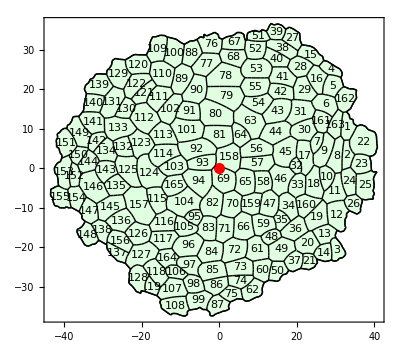

165 Cells

```mathematica
DQ=Tissue2DTissue[Q];
Print[Show[ShowTissue[DQ, Frame-> True, "CellNumbers"->True], Graphics[{Red, PointSize[.02], Point[{0,0}]}]]]; 
Print[n=NTissueCells[Q], " Cells"]
```

Define the Cellerator network that will produce the ODES as specified in the model

```mathematica
net={
{Y↦W,GRN[1/tauw,Twy,1,hw,sigma]},
{A↦W,GRN[1/tauw,Twa,1,hw,sigma]},
{W->∅,dw},
{Y->∅,dy},
{∅⇄A,a,beta},
{A+Y->Y,d},
{2 A+B->3 A,c},
{A->B,b},
{A⟶A, Diffusion[DA]},
{B⟶B, Diffusion[DB]}, 
{Y⟶Y, Diffusion[DY,DY]}
};
```

### Set Randomized Initial Conditions on All variables

```mathematica
ric:=RandomReal[{0,1}];
ic[i_]:={A[i]->ric,B[i]->ric,W[i]->ric,Y[i]->ric};
myic=Flatten[ic/@Range[n]];
```

### Define the Tuned Parameters

```mathematica
parameters={d-> .5,DY-> 2,  Twy->-25,Twa->0.5,kz->0.2,dy->.1,dz->0.1,DZ->0.1,kD->3.0,tauw->10,dw->0.1,hw->0,a->0.1,b->0.2,beta->0.1,c->0.1,DA->1.5,DB->15.0};
```

### Run The Simulation

Simulation Completed at t = 1000. after 0 cell divisions; Normal Exit. CPU: 95.718

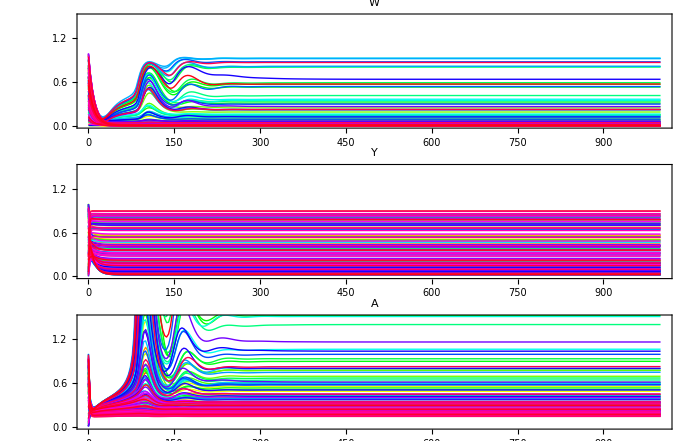

```mathematica
tmax=1000;
S=StaticSimulation[DQ,0,tmax,
 "tip"->False,
"xy"-> True, 
"CellVariable"-> area, 
"Internal"-> True, "Save"-> False, "Show"-> False, 
"Parameters"->parameters,
"Reactions"->net,"IC"->myic,
"TestCase"->"Wuschel",
"BoundaryConditions"->{Y->1}, 
"Verbose"->False];
GraphicsColumn[SimPlot[S,#,{0,tmax},PlotRange->{0,1.5},AspectRatio->.2,"Points"->300]&/@{W,Y,A}, ImageSize-> 700]
```

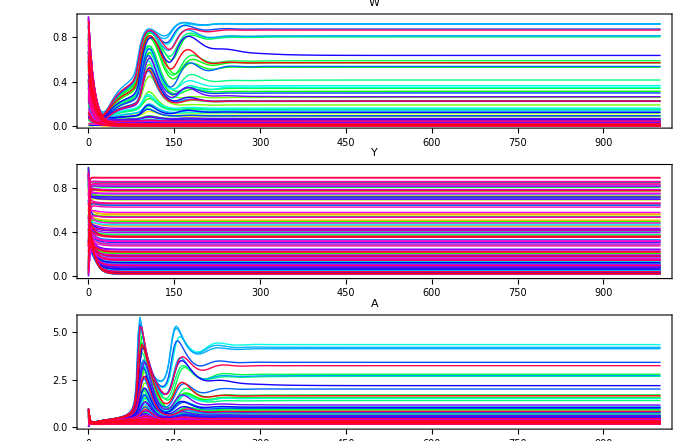

```mathematica
GraphicsColumn[SimPlot[S,#,{0,tmax},PlotRange->All,AspectRatio->.2,"Points"->300]&/@{W,Y,A}, ImageSize-> 700]
```

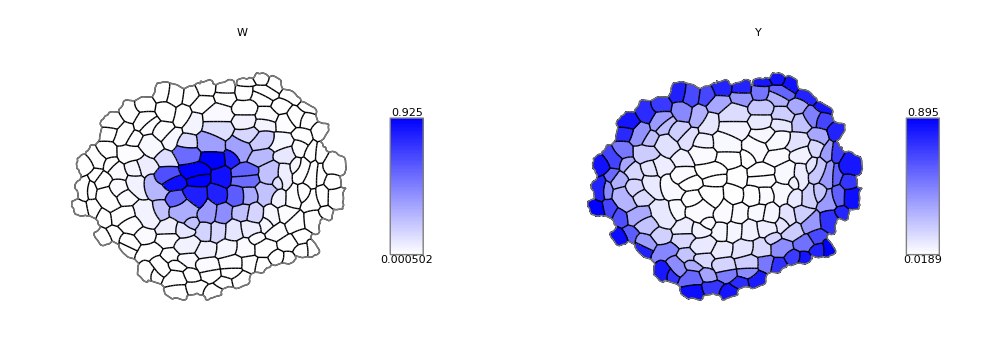

```mathematica
finalpic=GraphicsRow[SimShowFinal[S,#,DQ,{White,Blue}, PlotLabel-> #]&/@{W,Y},ImageSize-> 1000]
```

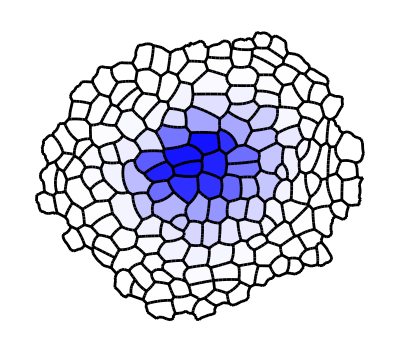

```mathematica
wusplot=SimShow[S, W, tmax, DQ, {White, Blue}, {0, 1}, "EdgeStyles"-> Directive[Thickness[.005]]]
```

```mathematica
Export[ToFileName[NotebookDirectory[],"Wuschel-D.eps"], wusplot, ImageSize-> 1800]
```

## Do Ablated Simulation

### Ablate all cells that have centers within 17 microns of the origin (the red dot in the very first picture) (There is nothing special about 17, it is just something chosen to make a sufficiently BIG hole in the center)

```mathematica
n=NTissueCells[Q];
cen=(#<17)&/@Norm/@Centroid[Q];
centercells=Pick[Range[n],cen]
```

{46,47,56,57,58,63,64,65,66,69,70,71,80,81,82,83,91,92,93,94,95,101,103,104,113,114,158,159,165}

### Create a new Tissue (and DTissue) with the cells ablated

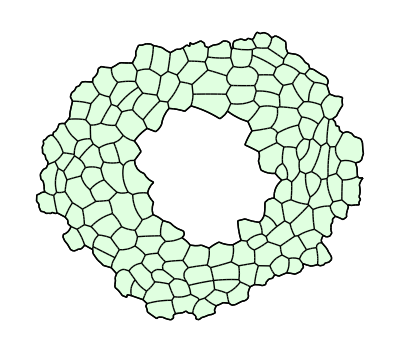

```mathematica
{vertices, edges, cells}=Q/.{Tissue-> List};
newcells=Delete[cells, List/@centercells];
QA=Tissue[vertices, edges,  newcells];
DQA=Tissue2DTissue[QA];
ShowTissue[DQA]
```

### Find the Union of the ablated cells to get the edge numbers of the ablated space

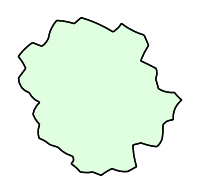

```mathematica
TTE="Edges"/.BoundaryCell[Tissue[vertices,edges, cells[[centercells]]]];
TT=Tissue[vertices, edges, {TTE}];
ShowTissue[TT,"ImageSize"-> 200]
```

### Show a list of the edge numbers of the abated shape.

```mathematica
TTE
```

{637,639,640,641,1259,1257,1258,1268,1261,1260,1255,1256,1262,1263,1264,1265,1266,1600,1599,1601,1602,1603,1604,1605,1606,1318,1317,1319,1322,1320,1321,1328,1329,1371,1572,1571,1569,1570,1643,1644,1645,1646,1647,1648,1649,1636,1520,1519,1593,1592,1522,1521,1537,1524,1523,1525,1526,1527,1528,1529,1530,1531,1159,1158,1160,1161,1162,1163,1164,1165,1166,1167,1173,1014,1013,1015,1016,1017,1018,1019,1020,1021,1022,1031,1032,1033,1034,1035,1044,1045,1046,1047,1048,1049,1086,1084,1085,1099,1100,1101,1123,1125,1126,1127,1128,1129,1130,1116,1115,1117,1118,1119,1120,1660,1661,1662,1666,1665,1667,1668,1669,1670,1671,645,644,646,638}

### Define an “impermeable” boundary on the edge of the ablated area to override the built in Boundary Condition that must be the same everywhere

```mathematica
Ablation[p_,q_,r_]:= If[MemberQ[TTE,r],0.0, 1.0]
```

```mathematica
anet={
{Y↦W,GRN[1/tauw,Twy,1,hw,sigma]},
{A↦W,GRN[1/tauw,Twa,1,hw,sigma]},
{W->∅,dw},
{Y->∅,dy},
{∅⇄A,a,beta},
{A+Y->Y,d},
{2 A+B->3 A,c},
{A->B,b},
{A⟶A,  Diffusion[DA]},
{B⟶B, Diffusion[DB]}, 
{Y⟶Y, Diffusion[DY, DY*Ablation[#1,#2,#3]&]}
};
```

### The tisse is smaller so need to redefine the initial conditions

```mathematica
n=NTissueCells[DQA]
```

136

```mathematica
ic[i_]:={A[i]->0,B[i]->0,W[i]->0,Y[i]->0};
myic=Flatten[ic/@Range[n]];
```

```mathematica
parameters={d-> .5,DY-> 2,  Twy->-25,Twa->0.5,kz->0.2,dy->.1,dz->0.1,DZ->0.1,kD->3.0,tauw->10,dw->0.1,hw->0,a->0.1,b->0.2,beta->0.1,c->0.1,DA->1.5,DB->15.0};
```

### rerun the simulation with the ablated system

Cellzilla2D (3.0.42 (26-May-2013)) loaded Fri 5 Jul 2013 13:34:18
using xCellerator 0.92a and XSSA 1204002
GPL License Terms Apply

Simulation Completed at t = 1000. after 0 cell divisions; Normal Exit. CPU: 78.6329

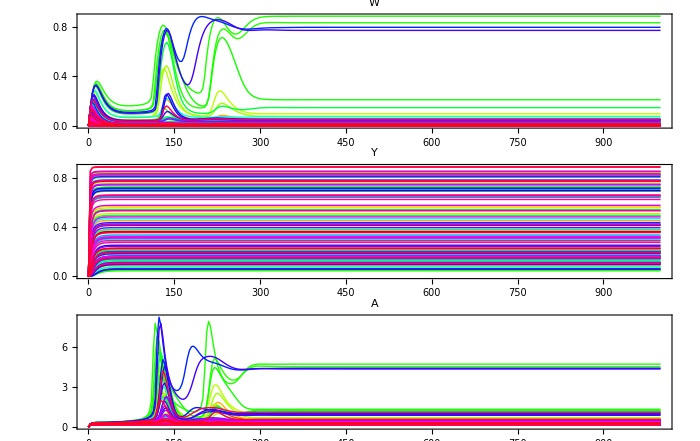

```mathematica
<<Cellzilla2D.m;
 tmax=1000;
 SA=StaticSimulation[DQA,0,tmax,
 "tip"->False,
"xy"-> True, 
"CellVariable"-> area, 
"Internal"-> True, "Save"-> False, "Show"-> False, 
"Parameters"->parameters,
"Reactions"->anet,"IC"->myic,
"TestCase"->"Wuschel",
"BoundaryConditions"->{Y->1},
"Verbose"->False];
GraphicsColumn[SimPlot[SA,#,{0,tmax},PlotRange->All,AspectRatio->.2,"Points"->300]&/@{W,Y,A}, ImageSize-> 700]
```

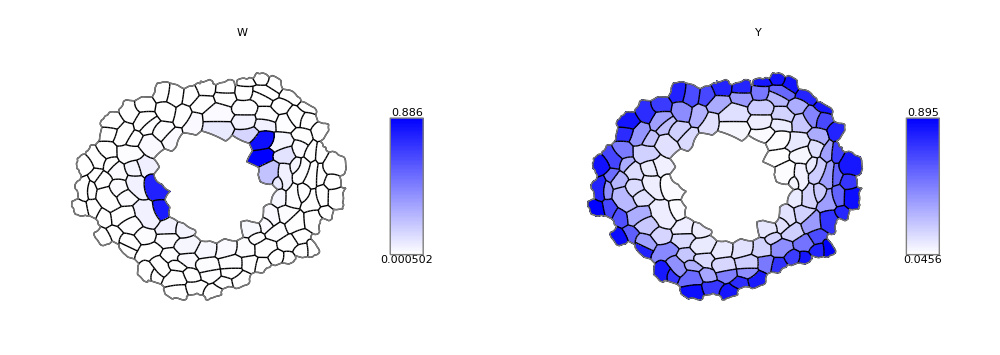

```mathematica
GraphicsRow[SimShowFinal[SA,#,DQA,{White,Blue}, PlotLabel-> #]&/@{W,Y},ImageSize-> 1000]
```

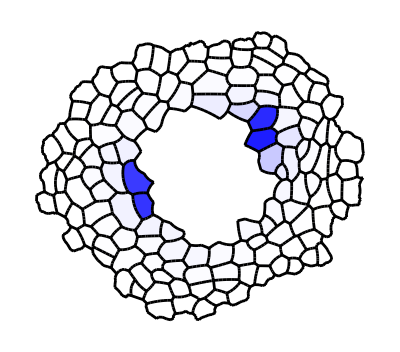

```mathematica
ablplot=SimShow[SA, W, tmax, DQA, {White, Blue}, {0, 1}, "EdgeStyles"-> Directive[Thickness[.005]]]
```

```mathematica
Export[ToFileName[NotebookDirectory[],"WuschelAbl-D.eps"], ablplot, ImageSize-> 1800]
```

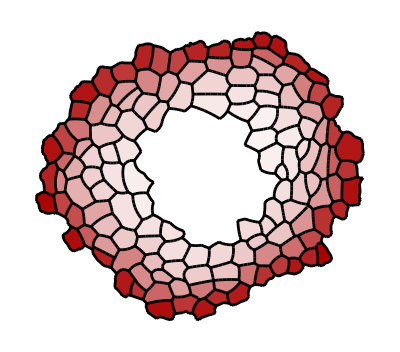

```mathematica
yplot=SimShow[SA, Y, 200, DQA, {White, Darker[Red]}, {0, .9}, "EdgeStyles"-> Directive[Thickness[.005]]]
```

```mathematica
Export[ToFileName[NotebookDirectory[],"WuschelY-D.eps"], yplot, ImageSize-> 1800]
```